We attempt to solve the full dispersion relation

```mathematica
hminus = ReplaceAll[1/2((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))/(L ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2))-√(((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))^2+4 ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2) (L^2 (γ̄)^10+c^4 K^4 L^2 V^6 Subscript[k, x]^6+L^2 (γ̄)^8 ((2 c^2+3 V^2) Subscript[k, x]^2+2 (c^2+V^2) Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 ((c^4+6 c^2 V^2+3 V^4) Subscript[k, x]^2+(c^2+V^2)^2 Subscript[k, y]^2)+K^2 V^2 (γ̄)^4 (L^2 (3 c^4+6 c^2 V^2+V^4) Subscript[k, x]^4+(c^2+V^2) (2 c^2+L^2 (3 c^2+V^2) Subscript[k, x]^2) Subscript[k, y]^2)+c^2 K^2 V^4 (γ̄)^2 Subscript[k, x]^2 (L^2 (3 c^2+2 V^2) Subscript[k, x]^4+(2 c^2+L^2 (3 c^2+2 V^2) Subscript[k, x]^2) Subscript[k, y]^2)))/(L^2 ((γ̄)^2+V^2 Subscript[k, x]^2)^2 ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2)^2 (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2)^2))),{c->√(P/ρ1),V->B/(√(μ*ρ1)),γ̄->(γ+I*kx*U1),L->(P/ρ1)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2)}];
```

```mathematica
ClearAll[ρ1,ρ2,P,U1,U2,g,kx,ky,B,μ,K]
```

```mathematica
hplus = ReplaceAll[1/2((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))/(L ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2))+√(((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))^2+4 ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2) (L^2 (γ̄)^10+c^4 K^4 L^2 V^6 Subscript[k, x]^6+L^2 (γ̄)^8 ((2 c^2+3 V^2) Subscript[k, x]^2+2 (c^2+V^2) Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 ((c^4+6 c^2 V^2+3 V^4) Subscript[k, x]^2+(c^2+V^2)^2 Subscript[k, y]^2)+K^2 V^2 (γ̄)^4 (L^2 (3 c^4+6 c^2 V^2+V^4) Subscript[k, x]^4+(c^2+V^2) (2 c^2+L^2 (3 c^2+V^2) Subscript[k, x]^2) Subscript[k, y]^2)+c^2 K^2 V^4 (γ̄)^2 Subscript[k, x]^2 (L^2 (3 c^2+2 V^2) Subscript[k, x]^4+(2 c^2+L^2 (3 c^2+2 V^2) Subscript[k, x]^2) Subscript[k, y]^2)))/(L^2 ((γ̄)^2+V^2 Subscript[k, x]^2)^2 ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2)^2 (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2)^2))),{c->√(P/ρ2),V->B/(√(μ*ρ2)),γ̄->(γ+I*kx*U2),L->(P/ρ2)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2)}];
```

```mathematica
disp=ReplaceAll[-(hminus (B^2 Subscript[c, 1]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 1]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))/(μ (Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)))+(hplus (B^2 Subscript[c, 2]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 2]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))/(μ (Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)))+g (-ρ1+ρ2+(Subscript[γ̄, 1]^2 (P μ (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+B^2 Subscript[c, 1]^2 ((-K^4+Subscript[k, x]^2 (K^2+Subscript[k, y]^2)) Subscript[V, 1]^2+Subscript[k, y]^2 Subscript[γ̄, 1]^2)))/(μ Subscript[c, 1]^2 (Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)))-(Subscript[γ̄, 2]^2 (P μ (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+B^2 Subscript[c, 2]^2 ((-K^4+Subscript[k, x]^2 (K^2+Subscript[k, y]^2)) Subscript[V, 2]^2+Subscript[k, y]^2 Subscript[γ̄, 2]^2)))/(μ Subscript[c, 2]^2 (Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)))),{Subscript[c, 2]->√(P/ρ2),Subscript[V, 2]->B/(√(μ*ρ2)),Subscript[γ̄, 2]->(γ+I*kx*U2),Subscript[L, 2]->(P/ρ2)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2),Subscript[c, 1]->√(P/ρ1),Subscript[V, 1]->B/(√(μ*ρ1)),Subscript[γ̄, 1]->(γ+I*kx*U1),Subscript[L, 1]->(P/ρ1)/g}]
```

-(hminus ((ⅈ kx U1+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ1) ((ⅈ kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (ⅈ kx U1+γ)^2)/(μ ρ1)))/(μ ((ⅈ kx U1+γ)^2 ((ⅈ kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((ⅈ kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+((kx^2+ky^2) P ((ⅈ kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (ⅈ kx U1+γ)^2)/(μ ρ1)))/ρ1))+(hplus ((ⅈ kx U2+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ2) ((ⅈ kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (ⅈ kx U2+γ)^2)/(μ ρ2)))/(μ ((ⅈ kx U2+γ)^2 ((ⅈ kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((ⅈ kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+((kx^2+ky^2) P ((ⅈ kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (ⅈ kx U2+γ)^2)/(μ ρ2)))/ρ2))+g (-ρ1+((ⅈ kx U1+γ)^2 (P μ ((ⅈ kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((ⅈ kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+(B^2 P (ky^2 (ⅈ kx U1+γ)^2+(B^2 (-(kx^2+ky^2)^2+kx^2 (kx^2+2 ky^2)))/(μ ρ1)))/ρ1) ρ1)/(P μ ((ⅈ kx U1+γ)^2 ((ⅈ kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((ⅈ kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+((kx^2+ky^2) P ((ⅈ kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (ⅈ kx U1+γ)^2)/(μ ρ1)))/ρ1))+ρ2-((ⅈ kx U2+γ)^2 (P μ ((ⅈ kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((ⅈ kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+(B^2 P (ky^2 (ⅈ kx U2+γ)^2+(B^2 (-(kx^2+ky^2)^2+kx^2 (kx^2+2 ky^2)))/(μ ρ2)))/ρ2) ρ2)/(P μ ((ⅈ kx U2+γ)^2 ((ⅈ kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((ⅈ kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+((kx^2+ky^2) P ((ⅈ kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (ⅈ kx U2+γ)^2)/(μ ρ2)))/ρ2)))

```mathematica
disprel[ρ1_,ρ2_,P_,U1_,U2_,g_,kx_,ky_,B_,μ_]:=-((((ⅈ kx U1+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ1) ((ⅈ kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (ⅈ kx U1+γ)^2)/(μ ρ1)) ((g ((ⅈ kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (ⅈ kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (ⅈ kx U1+γ)^8)/ρ1) ρ1)/(P ((ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)))-√((g^2 (((ⅈ kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (ⅈ kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (ⅈ kx U1+γ)^8)/ρ1)^2+4 ((ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ1^7)+(B^4 kx^2 (kx^2+ky^2) P (ⅈ kx U1+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1)+(kx^4 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)))/(μ^2 ρ1^3)+(P^2 (ⅈ kx U1+γ)^10)/(g^2 ρ1^2)+((kx^2+ky^2) P^2 (ⅈ kx U1+γ)^6 (kx^2 (P^2/ρ1^2+(3 B^4)/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2))+ky^2 (P/ρ1+B^2/(μ ρ1))^2))/(g^2 ρ1^2)+(P^2 (ⅈ kx U1+γ)^8 (2 ky^2 (P/ρ1+B^2/(μ ρ1))+kx^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(g^2 ρ1^2)+(B^2 (kx^2+ky^2) (ⅈ kx U1+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+B^2/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1) (P/ρ1+B^2/(μ ρ1))+(kx^4 P^2 ((3 P^2)/ρ1^2+B^4/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2)))/(g^2 ρ1^2)))/(μ ρ1))) ρ1^2)/(P^2 ((ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2))^2 ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2))^2 ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1))^2))))/(2 μ ((ⅈ kx U1+γ)^2 ((ⅈ kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((ⅈ kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+((kx^2+ky^2) P ((ⅈ kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (ⅈ kx U1+γ)^2)/(μ ρ1)))/ρ1)))+g (-ρ1+((ⅈ kx U1+γ)^2 (P μ ((ⅈ kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((ⅈ kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+(B^2 P (ky^2 (ⅈ kx U1+γ)^2+(B^2 (-(kx^2+ky^2)^2+kx^2 (kx^2+2 ky^2)))/(μ ρ1)))/ρ1) ρ1)/(P μ ((ⅈ kx U1+γ)^2 ((ⅈ kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((ⅈ kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+((kx^2+ky^2) P ((ⅈ kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (ⅈ kx U1+γ)^2)/(μ ρ1)))/ρ1))+ρ2-((ⅈ kx U2+γ)^2 (P μ ((ⅈ kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((ⅈ kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+(B^2 P (ky^2 (ⅈ kx U2+γ)^2+(B^2 (-(kx^2+ky^2)^2+kx^2 (kx^2+2 ky^2)))/(μ ρ2)))/ρ2) ρ2)/(P μ ((ⅈ kx U2+γ)^2 ((ⅈ kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((ⅈ kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+((kx^2+ky^2) P ((ⅈ kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (ⅈ kx U2+γ)^2)/(μ ρ2)))/ρ2)))+(((ⅈ kx U2+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ2) ((ⅈ kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (ⅈ kx U2+γ)^2)/(μ ρ2)) ((g ((ⅈ kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (ⅈ kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (ⅈ kx U2+γ)^8)/ρ2) ρ2)/(P ((ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)))+√((g^2 (((ⅈ kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (ⅈ kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (ⅈ kx U2+γ)^8)/ρ2)^2+4 ((ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ2^7)+(B^4 kx^2 (kx^2+ky^2) P (ⅈ kx U2+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2)+(kx^4 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)))/(μ^2 ρ2^3)+(P^2 (ⅈ kx U2+γ)^10)/(g^2 ρ2^2)+((kx^2+ky^2) P^2 (ⅈ kx U2+γ)^6 (kx^2 (P^2/ρ2^2+(3 B^4)/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2))+ky^2 (P/ρ2+B^2/(μ ρ2))^2))/(g^2 ρ2^2)+(P^2 (ⅈ kx U2+γ)^8 (2 ky^2 (P/ρ2+B^2/(μ ρ2))+kx^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(g^2 ρ2^2)+(B^2 (kx^2+ky^2) (ⅈ kx U2+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+B^2/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2) (P/ρ2+B^2/(μ ρ2))+(kx^4 P^2 ((3 P^2)/ρ2^2+B^4/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2)))/(g^2 ρ2^2)))/(μ ρ2))) ρ2^2)/(P^2 ((ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2))^2 ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2))^2 ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2))^2))))/(2 μ ((ⅈ kx U2+γ)^2 ((ⅈ kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((ⅈ kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+((kx^2+ky^2) P ((ⅈ kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (ⅈ kx U2+γ)^2)/(μ ρ2)))/ρ2));
```

```mathematica
dispnob[c1_,c2_,U1_,U2_,g_,kx_,ky_] := -1/c1^2+1/c2^2+((I kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(I kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(I kx U1+γ)^2))+((I kx U2+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(I kx U2+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(I kx U2+γ)^2));
```

```mathematica
disp2=ReplaceAll[(hplus (Subscript[k, x]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (B^2 Subscript[c, 2]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 2]^2))/(K^2 Subscript[c, 2]^2 Subscript[k, x]^2 Subscript[V, 2]^2+K^2 (Subscript[c, 2]^2+Subscript[V, 2]^2) Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)-(hminus (Subscript[k, x]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (B^2 Subscript[c, 1]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 1]^2))/(K^2 Subscript[c, 1]^2 Subscript[k, x]^2 Subscript[V, 1]^2+K^2 (Subscript[c, 1]^2+Subscript[V, 1]^2) Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)+g ((K^2 P μ Subscript[k, x]^2 Subscript[V, 2]^2+(K^2 P μ+B^2 Subscript[k, y]^2) Subscript[γ̄, 2]^2)/(K^2 Subscript[c, 2]^2 Subscript[k, x]^2 Subscript[V, 2]^2+K^2 (Subscript[c, 2]^2+Subscript[V, 2]^2) Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)-(K^2 P μ Subscript[k, x]^2 Subscript[V, 1]^2+(K^2 P μ+B^2 Subscript[k, y]^2) Subscript[γ̄, 1]^2)/(K^2 Subscript[c, 1]^2 Subscript[k, x]^2 Subscript[V, 1]^2+K^2 (Subscript[c, 1]^2+Subscript[V, 1]^2) Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)),{Subscript[c, 2]->√(P/ρ2),Subscript[V, 2]->B/(√(μ*ρ2)),Subscript[γ̄, 2]->(γ+I*kx*U2),Subscript[L, 2]->(P/ρ2)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2),Subscript[c, 1]->√(P/ρ1),Subscript[V, 1]->B/(√(μ*ρ1)),Subscript[γ̄, 1]->(γ+I*kx*U1),Subscript[L, 1]->(P/ρ1)/g}]
```

-((((ⅈ kx U1+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ1) ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)) ((g ((ⅈ kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (ⅈ kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (ⅈ kx U1+γ)^8)/ρ1) ρ1)/(P ((ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)))-√((g^2 (((ⅈ kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (ⅈ kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (ⅈ kx U1+γ)^8)/ρ1)^2+4 ((ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ1^7)+(B^4 kx^2 (kx^2+ky^2) P (ⅈ kx U1+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1)+(kx^4 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)))/(μ^2 ρ1^3)+(P^2 (ⅈ kx U1+γ)^10)/(g^2 ρ1^2)+((kx^2+ky^2) P^2 (ⅈ kx U1+γ)^6 (kx^2 (P^2/ρ1^2+(3 B^4)/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2))+ky^2 (P/ρ1+B^2/(μ ρ1))^2))/(g^2 ρ1^2)+(P^2 (ⅈ kx U1+γ)^8 (2 ky^2 (P/ρ1+B^2/(μ ρ1))+kx^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(g^2 ρ1^2)+(B^2 (kx^2+ky^2) (ⅈ kx U1+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+B^2/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1) (P/ρ1+B^2/(μ ρ1))+(kx^4 P^2 ((3 P^2)/ρ1^2+B^4/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2)))/(g^2 ρ1^2)))/(μ ρ1))) ρ1^2)/(P^2 ((ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2))^2 ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2))^2 ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1))^2))))/(2 ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2))))+g (-((ⅈ kx U1+γ)^2 (B^2 ky^2+(kx^2+ky^2) P μ)+(B^2 kx^2 (kx^2+ky^2) P)/ρ1)/((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2))+((ⅈ kx U2+γ)^2 (B^2 ky^2+(kx^2+ky^2) P μ)+(B^2 kx^2 (kx^2+ky^2) P)/ρ2)/((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)))+(((ⅈ kx U2+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ2) ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)) ((g ((ⅈ kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (ⅈ kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (ⅈ kx U2+γ)^8)/ρ2) ρ2)/(P ((ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)))+√((g^2 (((ⅈ kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (ⅈ kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (ⅈ kx U2+γ)^8)/ρ2)^2+4 ((ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ2^7)+(B^4 kx^2 (kx^2+ky^2) P (ⅈ kx U2+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2)+(kx^4 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)))/(μ^2 ρ2^3)+(P^2 (ⅈ kx U2+γ)^10)/(g^2 ρ2^2)+((kx^2+ky^2) P^2 (ⅈ kx U2+γ)^6 (kx^2 (P^2/ρ2^2+(3 B^4)/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2))+ky^2 (P/ρ2+B^2/(μ ρ2))^2))/(g^2 ρ2^2)+(P^2 (ⅈ kx U2+γ)^8 (2 ky^2 (P/ρ2+B^2/(μ ρ2))+kx^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(g^2 ρ2^2)+(B^2 (kx^2+ky^2) (ⅈ kx U2+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+B^2/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2) (P/ρ2+B^2/(μ ρ2))+(kx^4 P^2 ((3 P^2)/ρ2^2+B^4/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2)))/(g^2 ρ2^2)))/(μ ρ2))) ρ2^2)/(P^2 ((ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2))^2 ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2))^2 ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2))^2))))/(2 ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)))

```mathematica
disprel2[ρ1_,ρ2_,P_,U1_,U2_,g_,kx_,ky_,B_,μ_]:=-((((ⅈ kx U1+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ1) ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)) ((g ((ⅈ kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (ⅈ kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (ⅈ kx U1+γ)^8)/ρ1) ρ1)/(P ((ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)))-√((g^2 (((ⅈ kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (ⅈ kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (ⅈ kx U1+γ)^8)/ρ1)^2+4 ((ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ1^7)+(B^4 kx^2 (kx^2+ky^2) P (ⅈ kx U1+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1)+(kx^4 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)))/(μ^2 ρ1^3)+(P^2 (ⅈ kx U1+γ)^10)/(g^2 ρ1^2)+((kx^2+ky^2) P^2 (ⅈ kx U1+γ)^6 (kx^2 (P^2/ρ1^2+(3 B^4)/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2))+ky^2 (P/ρ1+B^2/(μ ρ1))^2))/(g^2 ρ1^2)+(P^2 (ⅈ kx U1+γ)^8 (2 ky^2 (P/ρ1+B^2/(μ ρ1))+kx^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(g^2 ρ1^2)+(B^2 (kx^2+ky^2) (ⅈ kx U1+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+B^2/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1) (P/ρ1+B^2/(μ ρ1))+(kx^4 P^2 ((3 P^2)/ρ1^2+B^4/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2)))/(g^2 ρ1^2)))/(μ ρ1))) ρ1^2)/(P^2 ((ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2))^2 ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2))^2 ((ⅈ kx U1+γ)^2+(B^2 kx^2)/(μ ρ1))^2))))/(2 ((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2))))+g (-((ⅈ kx U1+γ)^2 (B^2 ky^2+(kx^2+ky^2) P μ)+(B^2 kx^2 (kx^2+ky^2) P)/ρ1)/((ⅈ kx U1+γ)^4+(kx^2+ky^2) (ⅈ kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2))+((ⅈ kx U2+γ)^2 (B^2 ky^2+(kx^2+ky^2) P μ)+(B^2 kx^2 (kx^2+ky^2) P)/ρ2)/((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)))+(((ⅈ kx U2+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ2) ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)) ((g ((ⅈ kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (ⅈ kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (ⅈ kx U2+γ)^8)/ρ2) ρ2)/(P ((ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)))+√((g^2 (((ⅈ kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (ⅈ kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (ⅈ kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (ⅈ kx U2+γ)^8)/ρ2)^2+4 ((ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ2^7)+(B^4 kx^2 (kx^2+ky^2) P (ⅈ kx U2+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2)+(kx^4 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)))/(μ^2 ρ2^3)+(P^2 (ⅈ kx U2+γ)^10)/(g^2 ρ2^2)+((kx^2+ky^2) P^2 (ⅈ kx U2+γ)^6 (kx^2 (P^2/ρ2^2+(3 B^4)/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2))+ky^2 (P/ρ2+B^2/(μ ρ2))^2))/(g^2 ρ2^2)+(P^2 (ⅈ kx U2+γ)^8 (2 ky^2 (P/ρ2+B^2/(μ ρ2))+kx^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(g^2 ρ2^2)+(B^2 (kx^2+ky^2) (ⅈ kx U2+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+B^2/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2) (P/ρ2+B^2/(μ ρ2))+(kx^4 P^2 ((3 P^2)/ρ2^2+B^4/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2)))/(g^2 ρ2^2)))/(μ ρ2))) ρ2^2)/(P^2 ((ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2))^2 ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2))^2 ((ⅈ kx U2+γ)^2+(B^2 kx^2)/(μ ρ2))^2))))/(2 ((ⅈ kx U2+γ)^4+(kx^2+ky^2) (ⅈ kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)))
```

#### Solve Equation

With the below parameters gptips2 got a fit of -0.01519 B^3 + 0.00489 B^2 + 2.148*10^-5, imaginary component seems to go as (a*B^4 + b*B^2 + c)/(B^2 + d)

```mathematica
wp=250;
ρ2=SetPrecision[8*10^-8,wp];
ρ1=SetPrecision[3*10^-7,wp];
U1 = SetPrecision[0,wp];
U2 =SetPrecision[ 500000,wp];
d=SetPrecision[U2-U1,wp];
(*d = U2-U1;*)
P=SetPrecision[200,wp];
A=SetPrecision[(ρ1-ρ2)/(ρ1+ρ2),wp];
c1 =SetPrecision[ √(P/ρ1),wp];
c2=SetPrecision[ √(P/ρ2),wp];
B =SetPrecision[0.00001,wp];
μ=SetPrecision[4*π*10^-7,wp];
g=SetPrecision[10,wp];
kx=SetPrecision[1,wp];
ky=SetPrecision[0,wp];
```

```mathematica
gammaincomp[ρ1_,ρ2_,U1_,U2_,kx_,g_,B_]:=I*( -kx(ρ1/(ρ1+ρ2)U1+ρ2/(ρ1+ρ2)U2)-√(-g *kx*(ρ1-ρ2)/(ρ1+ρ2)+kx^2 *(2*B^2)/(4*π*10^-7*(ρ1+ρ2))-kx^2*(ρ1*ρ2)/(ρ1+ρ2)^2(U1-U2)^2));
```

```mathematica
ReplaceAll[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2)),{c1->(P/ρ1)^(1/2),c2->(P/ρ2)^(1/2)}]
```

-ρ1/P+((ⅈ kx U1+γ)^2 (1+√(1+(4 P ((ⅈ kx U1+γ)^2+((kx^2+ky^2) P)/ρ1))/(g^2 ρ1))) ρ1)/(2 P ((ⅈ kx U1+γ)^2+((kx^2+ky^2) P)/ρ1))+ρ2/P+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 P ((ⅈ kx (d+U1)+γ)^2+((kx^2+ky^2) P)/ρ2))/(g^2 ρ2))) ρ2)/(2 P ((ⅈ kx (d+U1)+γ)^2+((kx^2+ky^2) P)/ρ2))

```mathematica
disprelnob[ρ1_,ρ2_,P_,U1_,U2_,g_,kx_,ky_]:=-ρ1/P+((ⅈ kx U1+γ)^2 (1+√(1+(4 P ((ⅈ kx U1+γ)^2+((kx^2+ky^2) P)/ρ1))/(g^2 ρ1))) ρ1)/(2 P ((ⅈ kx U1+γ)^2+((kx^2+ky^2) P)/ρ1))+ρ2/P+((ⅈ kx (U2)+γ)^2 (-1+√(1+(4 P ((ⅈ kx (U2)+γ)^2+((kx^2+ky^2) P)/ρ2))/(g^2 ρ2))) ρ2)/(2 P ((ⅈ kx (U2)+γ)^2+((kx^2+ky^2) P)/ρ2));
```

```mathematica
khapprox [g_,c1_,c2_,d_,kx_,U1_]:=(g*c2)/(2*c1*d)-kx(c1+U1)*I;
```

```mathematica
rtapprox[g_,c1_,c2_,d_,kx_,U1_]:=g/2(1/c1-1/c2)-I*kx*(c1*d/(c1+c2)+U1);
```

#### Use this one below to start from no magnetic field. First is KH, second is RT.

```mathematica
wp=850;
μ=SetPrecision[4*π*10^-7,wp];
list = {};
Do[
exitvalue = 1;
test = SetPrecision[khapprox [SetPrecision[g,wp],SetPrecision[√(P/ρ1),wp],SetPrecision[ √(P/ρ2),wp],SetPrecision[d,wp],SetPrecision[kx,wp],SetPrecision[U1,wp]],wp];
Do[
If[exitvalue<1*10^-10,Break[]];
result =FindRoot[SetPrecision[disprel[SetPrecision[ρ1,wp],SetPrecision[ρ2,wp],SetPrecision[P,wp],SetPrecision[U1,wp],SetPrecision[d+U1,wp],SetPrecision[g,wp],SetPrecision[kx,wp],SetPrecision[ky,wp],SetPrecision[B,wp],μ],wp]==0,{γ,test},WorkingPrecision->wp,AccuracyGoal->150,PrecisionGoal->150,MaxIterations->20000];
AppendTo[list,{ρ1,ρ2,P,N[√(P/ρ1)],N[√(P/ρ2)],U1,d,N[d/(√(P/ρ1)+√(P/ρ2))],g,kx,ky,B,(2*P*μ)/B^2,Re[result[[1,2]]],Im[result[[1,2]]]}];
test = result[[1,2]];
exitvalue=Abs[Re[result[[1,2]]]],
{B,0.00001,0.00002,0.00001}
 ],
{kx,1,1,1},
{ky,0,0,1},
{g,10,10,10},
{d,1000000,1000000,100000},
{U1,0,0,10000},
{P,200,200,10},
{ρ2,8*10^-8,8*10^-8,1*10^-8},
{ρ1,3*10^-7,3*10^-7,1*10^-7}]
```

```mathematica
list
```

{{3/10000000,1/12500000,200,25819.9,50000.,0,1000000,13.1892,10,1,0,0.00001,5.02655×10^6,-9.947128606804155040516534999091476594148655537843613624746851332202281619350849538420860443450263532028771397044727488189233004362799671831013104731609347959884583919877819853132884065054350276956764048973061308887923222242922706273667329847945866484697185142019297873265506453132813314748859050157272366793289615768329743176746983343758339763244356571425871297992086818305020562575927894176563626206442819778592698537445303959875724047637120879457676925798658213103718688605955180760611313290084101469551190930616304275625628370406681078810367148004293567208795710993638530990076632682365317348857722171542443187190855116821136179087847747086529486536843776057702018240339197119046911876224752373273783777588107893016088282875478553861662599458687260472603286901762176973092323938645062772583769956965022853295552599020974587497889418964323507265959×10^-6,-25853.96704878550488061049363543304701592876351972839536014382940603882644406700498927518112175700111728363747221870524528493356275318775190059558859358966128834403227016944469399180396353508436106178723895740529427177488687874195043619770907740856150075802442500193081437777749771025386069371832779251568926430416089724971119865300057554621085463829363107695996011557312393329092688099884326599188401089243858445931121836750299916036029461104248343285521908869776196652924283567849558257263899778063021996005202047350595410848549434197750466057137076103585676472557183845440880098145122734380138808619476300093192275400446713890395747341525774147261680343449962651624224052105426959445655797957008050237094848389604757257792713462356776191739568891283288332601485078588506426581624421757036266072983993848758803091943488571103858345850939624458343726},{3/10000000,1/12500000,200,25819.9,50000.,0,1000000,13.1892,10,1,0,0.00002,1.25664×10^6,-9.94712271352925433690026621421960859728662883873624342764562942852153193194473607559446038206172845746640630410163665375002400215429025021071430420987552803122241957116590683909674797374713084528120198379719119864788149166378565490562476811518514245032110399650735224794591325102478385020064596148813346601047306142342813553177694261588574345582936945019825413628042620481924286020904197188026668140724942037583542130901248753672636369179902382870003119746335154467017705578439462782206352245697810343931062227869123027327623974326483932531319217907707938139099419866962672467432226574100393713180511148379139662304579668947747618828273799242344081341453004767371186042437078999377353008841029882880544349763421037994823394313028836383078394267392624213162045288112356183494723481090850800975698252739451193449615330655607159202740415403266514573415×10^-6,-25853.96696747811000392939696640616227494696031874661410156727641794267621816776463407032491572549735850736259833093479510711961230587297573442299004041515911243860052045257008970652697390171417852696976655666898948533942946658620661651669767351100979985375225803886999131798656064019161312887173873516421307344968691743238037069275236407888178260963661107820797662723063900571271672627345477921789371257838141136928883345907791634508253001078156220894386543154805575751469631015429538113291060065254235990635280141780500411076008675805517443234436305793972405207114907340368206283290644461069581281710656854630049783172757374640040082878324813126354915598517342106246888229427638343779666761752010986754096800227045664940518085960105259790154232092930797703999036565692987626983129019855006322816332804046968336324179142154978726530607312043100152844}}

```mathematica
wp=850;
μ=SetPrecision[4*π*10^-7,wp];
list = {};
Do[
exitvalue = 1;
test = SetPrecision[khapprox [SetPrecision[g,wp],SetPrecision[√(P/ρ1),wp],SetPrecision[ √(P/ρ2),wp],SetPrecision[d,wp],SetPrecision[kx,wp],SetPrecision[U1,wp]],wp];
Do[
If[exitvalue<1*10^-10,Break[]];
result =FindRoot[SetPrecision[disprel2[SetPrecision[ρ1,wp],SetPrecision[ρ2,wp],SetPrecision[P,wp],SetPrecision[U1,wp],SetPrecision[d+U1,wp],SetPrecision[g,wp],SetPrecision[kx,wp],SetPrecision[ky,wp],SetPrecision[B,wp],μ],wp]==0,{γ,test},WorkingPrecision->wp,AccuracyGoal->150,PrecisionGoal->150,MaxIterations->20000];
result2 =FindRoot[SetPrecision[disprel2[SetPrecision[ρ1,wp],SetPrecision[ρ2,wp],SetPrecision[P,wp],SetPrecision[U1,wp],SetPrecision[d+U1,wp],SetPrecision[g,wp],SetPrecision[kx,wp],SetPrecision[ky,wp],SetPrecision[B,wp],μ],wp]==0,{γ,test},WorkingPrecision->wp,AccuracyGoal->150,PrecisionGoal->150,MaxIterations->20000];
AppendTo[list,{ρ1,ρ2,P,N[√(P/ρ1)],N[√(P/ρ2)],U1,d,N[d/(√(P/ρ1)+√(P/ρ2))],g,kx,ky,B,(2*P*μ)/B^2,Re[result[[1,2]]],Im[result[[1,2]]],Re[result[[1,2]]]-Re[result2[[1,2]]]}];
test = result[[1,2]];
exitvalue=Abs[Re[result[[1,2]]]],
{B,0.00001,0.00002,0.00001}
 ],
{kx,1,1,1},
{ky,0,0,1},
{g,10,10,10},
{d,1000000,1000000,100000},
{U1,0,0,10000},
{P,200,200,10},
{ρ2,8*10^-8,8*10^-8,1*10^-8},
{ρ1,3*10^-7,3*10^-7,1*10^-7}]
```

```mathematica
list
```

{{3/10000000,1/12500000,200,25819.9,50000.,0,1000000,13.1892,10,1,0,0.00001,5.02655×10^6,-9.947128606804155040516534999091476594148655537843613624746851332202281619350849538420860443450263532028771397044727488189233004362799671831013104731609347959884583919877819853132884065054350276956764048973061308887923222242922706273667329847945866484697185142019297873265506453132813314748859050157272366793289615768329743176746983343758339763244356571425871297992086818305020562575927894176563626206442819778592698537445303959875724047637120879457676925798658213103718688605955180760611313290084101469551190930616304275625628370406681078810367148004293567208795710993638530990076632682365317348857722171542443187190855116821136179087847747086529486536843776057702018240339197119046911876224752373273783777588107893016088282875478553861662599458687260472603286901762176973092323938645062772583769956965022853295552599020974587497889418964323507265959×10^-6,-25853.96704878550488061049363543304701592876351972839536014382940603882644406700498927518112175700111728363747221870524528493356275318775190059558859358966128834403227016944469399180396353508436106178723895740529427177488687874195043619770907740856150075802442500193081437777749771025386069371832779251568926430416089724971119865300057554621085463829363107695996011557312393329092688099884326599188401089243858445931121836750299916036029461104248343285521908869776196652924283567849558257263899778063021996005202047350595410848549434197750466057137076103585676472557183845440880098145122734380138808619476300093192275400446713890395747341525774147261680343449962651624224052105426959445655797957008050237094848389604757257792713462356776191739568891283288332601485078588506426581624421757036266072983993848758803091943488571103858345850939624458343726,0.},{3/10000000,1/12500000,200,25819.9,50000.,0,1000000,13.1892,10,1,0,0.00002,1.25664×10^6,-9.94712271352925433690026621421960859728662883873624342764562942852153193194473607559446038206172845746640630410163665375002400215429025021071430420987552803122241957116590683909674797374713084528120198379719119864788149166378565490562476811518514245032110399650735224794591325102478385020064596148813346601047306142342813553177694261588574345582936945019825413628042620481924286020904197188026668140724942037583542130901248753672636369179902382870003119746335154467017705578439462782206352245697810343931062227869123027327623974326483932531319217907707938139099419866962672467432226574100393713180511148379139662304579668947747618828273799242344081341453004767371186042437078999377353008841029882880544349763421037994823394313028836383078394267392624213162045288112356183494723481090850800975698252739451193449615330655607159202740415403266514573415×10^-6,-25853.96696747811000392939696640616227494696031874661410156727641794267621816776463407032491572549735850736259833093479510711961230587297573442299004041515911243860052045257008970652697390171417852696976655666898948533942946658620661651669767351100979985375225803886999131798656064019161312887173873516421307344968691743238037069275236407888178260963661107820797662723063900571271672627345477921789371257838141136928883345907791634508253001078156220894386543154805575751469631015429538113291060065254235990635280141780500411076008675805517443234436305793972405207114907340368206283290644461069581281710656854630049783172757374640040082878324813126354915598517342106246888229427638343779666761752010986754096800227045664940518085960105259790154232092930797703999036565692987626983129019855006322816332804046968336324179142154978726530607312043100152844,0.}}

```mathematica
{{3/10000000,1/12500000,200,25819.888974716112,50000.,0,1000000,13.189151468336664,10,1,0,0.00001,5.026548245743668*^6,-9.947128606804155040516534999091476594148655537843613624746851332202281619350849538420860443450263532028771397044727488189233004362799671831013104731609347959884583919877819853132884065054350276956764048973061308887923222242922706273667329847945866484697185142019297873265506453132813314748859050157272366793289615768329743176746983343758339763244356571425871297992086818305020562575927894176563626206442819778592698537445303959875724047637120879457676925798658213103718688605955180760611313290084101469551190930616304275625628370406681078810367148004293567208795710993638530990076632682365317348857722171542443187190855116821136179087847747086529486536843776057702018240339197119046911876224752373273783777588107893016088282875478553861662599458687260472603286901762176973092323938645062772583769956965022853295552599020974587497889418964323507265959112818873519`850.*^-6,-25853.967048785504880610493635433047015928763519728395360143829406038826444067004989275181121757001117283637472218705245284933562753187751900595588593589661288344032270169444693991803963535084361061787238957405294271774886878741950436197709077408561500758024425001930814377777497710253860693718327792515689264304160897249711198653000575546210854638293631076959960115573123933290926880998843265991884010892438584459311218367502999160360294611042483432855219088697761966529242835678495582572638997780630219960052020473505954108485494341977504660571370761035856764725571838454408800981451227343801388086194763000931922754004467138903957473415257741472616803434499626516242240521054269594456557979570080502370948483896047572577927134623567761917395688912832883326014850785885064265816244217570362660729839938487588030919434885711038583458509396244583437262481982873665655986486`850.},{3/10000000,1/12500000,200,25819.888974716112,50000.,0,1000000,13.189151468336664,10,1,0,0.00002,1.256637061435917*^6,-9.947122713529254336900266214219608597286628838736243427645629428521531931944736075594460382061728457466406304101636653750024002154290250210714304209875528031222419571165906839096747973747130845281201983797191198647881491663785654905624768115185142450321103996507352247945913251024783850200645961488133466010473061423428135531776942615885743455829369450198254136280426204819242860209041971880266681407249420375835421309012487536726363691799023828700031197463351544670177055784394627822063522456978103439310622278691230273276239743264839325313192179077079381390994198669626724674322265741003937131805111483791396623045796689477476188282737992423440813414530047673711860424370789993773530088410298828805443497634210379948233943130288363830783942673926242131620452881123561834947234810908508009756982527394511934496153306556071592027404154032665145734149786648014324`850.*^-6,-25853.966967478110003929396966406162274946960318746614101567276417942676218167764634070324915725497358507362598330934795107119612305872975734422990040415159112438600520452570089706526973901714178526969766556668989485339429466586206616516697673511009799853752258038869991317986560640191613128871738735164213073449686917432380370692752364078881782609636611078207976627230639005712716726273454779217893712578381411369288833459077916345082530010781562208943865431548055757514696310154295381132910600652542359906352801417805004110760086758055174432344363057939724052071149073403682062832906444610695812817106568546300497831727573746400400828783248131263549155985173421062468882294276383437796667617520109867540968002270456649405180859601052597901542320929307977039990365656929876269831290198550063228163328040469683363241791421549787265306073120431001528437311587697479662281073`850.}}
```

```mathematica
Length[list]
```

30891

#### Below is RT

```mathematica
wp=550;
μ=SetPrecision[4*π*10^-7,wp];
list = {};
Do[
exitvalue = 1;
test = SetPrecision[rtapprox [SetPrecision[g,wp],SetPrecision[√(P/ρ1),wp],SetPrecision[ √(P/ρ2),wp],SetPrecision[d,wp],SetPrecision[kx,wp],SetPrecision[U1,wp]],wp];
Do[
If[exitvalue<1*10^-10,Break[]];
result =FindRoot[SetPrecision[disprel[SetPrecision[ρ1,wp],SetPrecision[ρ2,wp],SetPrecision[P,wp],SetPrecision[U1,wp],SetPrecision[d+U1,wp],SetPrecision[g,wp],SetPrecision[kx,wp],SetPrecision[ky,wp],SetPrecision[B,wp],μ],wp]==0,{γ,test},WorkingPrecision->wp,AccuracyGoal->64,PrecisionGoal->64,MaxIterations->20000];
AppendTo[list,{ρ1,ρ2,P,N[√(P/ρ1)],N[√(P/ρ2)],U1,d,N[d/(√(P/ρ1)+√(P/ρ2))],g,kx,ky,B,(2*P*μ)/B^2,Re[result[[1,2]]],Im[result[[1,2]]]}];
test = result[[1,2]];
exitvalue=Abs[Re[result[[1,2]]]],
{B,0.00001,1,0.00001}
 ],
{kx,1,1,1},
{ky,0,0,1},
{g,10,10,10},
{d,500000,500000,10000},
{U1,0,0,10000},
{P,200,200,10},
{ρ2,8*10^-8,8*10^-8,1*10^-8},
{ρ1,6*10^-7,6*10^-7,1*10^-7}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 20000 iterations.

$Aborted

```mathematica
Length[list]
```

11613

b = 0.10954, c1 = 22360, rho1 = 4*10^-7
b = 0.11323, c1 = 20000, rho1 = 5*10^-7
b = 0.11612, c1 = 18257.4, rho1 = 6*10^-7

```mathematica
listb=list[[;;,12]];
listgam =list[[;;,14]];
listgamim = list[[;;,15]];
listdatatest = Thread[{listb,listgam}];
listdatatestim=Thread[{listb,listgamim}];
```

#### Use the one below to start with a specific magnetic field and known growthrate. In list 14 is re gam, 15 is im gam, b is 12

```mathematica
list[[1000]]
```

{3/10000000,1/12500000,200,25819.9,50000.,0,1000000,13.1892,10,1,0,0.01,5.02655,-8.420721504000955863598193244611910282948058286837840699004366476359638274772240378602019830335528104982757117428027584942949592813094728108002269812680911135033379390943227819277701344614202016791090584478807744084431636897730517448767473843916393924456177544334765350504356166399852757883669440468161923494293362081288794545216887593448455003553628794827377643903741911556296989514001637269521482010631363565524467653726880159510549632789820425482342927661602949583118198202635896726948163052984419610927405858042705066635753145753998733597284745114941277660652604691452233162909571286584997146710873427094771505204078849534638364299072208094370159381333378575217597246545819216956072736602550989177615221679961703808381502857356221240236814884956336472691149151935534180310642411409945361687256279138812279964256298459529123833006354208875751956213×10^-6,-25834.57237546535080869076343333811962692336133135805792620428125979460354487829005117867297009000311619687944125523557251409501158281500417197058871088962501186903809836612628693905180493028408479044539229850774173543397804002561515236929587855887901216331911778376563869517177470034538798379666149817595083546877684556673395485294426236726090083815850448916654590527892033453733068029555818325561886394880520728707332397182757601857946318812467478311108114780805561671466275032186608778957113550602163500355712671291150482046202802180575554363216274796131786504202237555647761575055242859278444334362972203803313231362169821395471907217464145883210323815579121262889193567497106021190879517653068712103747263404256904303881419154896947098337308810549146128509490553332587614302773268420606420791713700781598675470112693008611814764694369349572988581}

```mathematica
wp=350;
μ=SetPrecision[4*π*10^-7,wp];
worklist = {};
Do[
exitvalue = 1;
test = SetPrecision[Abs[list[[1000,14]]]+list[[1000,15]],wp];
Do[
If[exitvalue<1*10^-10,Break[]];
result =FindRoot[SetPrecision[disprel[SetPrecision[ρ1,wp],SetPrecision[ρ2,wp],SetPrecision[P,wp],SetPrecision[U1,wp],SetPrecision[d+U1,wp],SetPrecision[g,wp],SetPrecision[kx,wp],SetPrecision[ky,wp],SetPrecision[B,wp],μ],wp]==0,{γ,test},WorkingPrecision->wp,AccuracyGoal->64,PrecisionGoal->64,MaxIterations->50000];
AppendTo[worklist,{ρ1,ρ2,P,N[√(P/ρ1)],N[√(P/ρ2)],U1,d,N[d/(√(P/ρ1)+√(P/ρ2))],g,kx,ky,B,(2*P*μ)/B^2,Re[result[[1,2]]],Im[result[[1,2]]]}];
test = result[[1,2]];
exitvalue=Abs[Re[result[[1,2]]]],
{B,list[[1000,12]],list[[1000,12]],0.000001}
 ],
{kx,list[[1000,10]],list[[1000,10]],1},
{ky,list[[1000,11]],list[[1000,11]],0.001},
{g,list[[1000,9]],list[[1000,9]],10},
{d,list[[1000,7]],list[[1000,7]]+200000,10000},
{U1,list[[1000,6]],list[[1000,6]],10000},
{P,list[[1000,3]],list[[1000,3]],100},
{ρ2,list[[1000,2]],list[[1000,2]],1*10^-8},
{ρ1,list[[1000,1]],list[[1000,1]],1*10^-7}]
```

#### Plot results of specific variable scan

```mathematica
listd = worklist[[;;,7]];
listgamre =Abs[worklist[[;;,14]]];
listgamim=Abs[worklist[[;;,15]]];
listdatatestre = Thread[{listd,listgamre}];
listdatatestim = Thread[{listd,listgamim}];
```

```mathematica
ListPlot[listdatatestre]
```

```mathematica
ListPlot[listdatatestim]
```

#### Scan at low Mc

```mathematica
wp=850;
μ=SetPrecision[4*π*10^-7,wp];
```

```mathematica
SetPrecision[gammaincomp [SetPrecision[3*10^-7,wp],SetPrecision[8*10^-8,wp],SetPrecision[ 0,wp],SetPrecision[2000,wp],SetPrecision[1,wp],SetPrecision[10,wp],SetPrecision[0.00035,wp]],wp]
```

```mathematica
N[Solve[-240002090/361+(250000000000000 B^2)/(19 π)==0,B]]
```

{{B→-0.000398415},{B→0.000398415}}

```mathematica
gammaincomp[3*10^-7,8*10^-8,0,2000,1,10,0.00001]
```

815.112-421.053 ⅈ

```mathematica
disprel[SetPrecision[1/2000000,wp],SetPrecision[50/1900000921,wp],SetPrecision[200,wp],SetPrecision[0,wp],SetPrecision[10000,wp],SetPrecision[10,wp],SetPrecision[1,wp],SetPrecision[0,wp],SetPrecision[0,wp],μ]
```

```mathematica
FindRoot[SetPrecision[disprel[SetPrecision[3*10^-7,wp],SetPrecision[8*10^-8,wp],SetPrecision[200,wp],SetPrecision[0,wp],SetPrecision[2000,wp],SetPrecision[10,wp],SetPrecision[1,wp],SetPrecision[0,wp],SetPrecision[0.00025,wp],μ],wp]==0,{γ,1+I},WorkingPrecision->wp,AccuracyGoal->150,PrecisionGoal->150,MaxIterations->20000]
```

```mathematica
wp=850;
μ=SetPrecision[4*π*10^-7,wp];
list = {};
Do[
exitvalue = 1;
Do[
If[exitvalue<1*10^-10,Break[]];
test = SetPrecision[gammaincomp [SetPrecision[ρ1,wp],SetPrecision[ρ2,wp],SetPrecision[ U1,wp],SetPrecision[d+U1,wp],SetPrecision[kx,wp],SetPrecision[g,wp],SetPrecision[B,wp]],wp];
result =FindRoot[SetPrecision[disprel[SetPrecision[ρ1,wp],SetPrecision[ρ2,wp],SetPrecision[P,wp],SetPrecision[U1,wp],SetPrecision[d+U1,wp],SetPrecision[g,wp],SetPrecision[kx,wp],SetPrecision[ky,wp],SetPrecision[B,wp],μ],wp]==0,{γ,test},WorkingPrecision->wp,AccuracyGoal->150,PrecisionGoal->150,MaxIterations->20000];
AppendTo[list,{ρ1,ρ2,P,N[√(P/ρ1)],N[√(P/ρ2)],U1,d,N[d/(√(P/ρ1)+√(P/ρ2))],g,kx,ky,B,(2*P*μ)/B^2,Re[result[[1,2]]],Im[result[[1,2]]],N[(B/(√(μ*(ρ1+ρ2))))/d],Re[test],Im[test]}];
exitvalue=Abs[Re[result[[1,2]]]],
{B,0.000001,0.000399,0.000001}
 ],
{kx,1,1,1},
{ky,0,0,1},
{g,10,10,10},
{d,2000,2000,2000},
{U1,0,0,10000},
{P,200,200,10},
{ρ2,8*10^-8,8*10^-8,1*10^-8},
{ρ1,3*10^-7,3*10^-7,1*10^-7}]
```

#### Plot results of low Mc scan of B

```mathematica
listalf = list[[;;,16]];
listgamc = Rescale[Abs[list[[;;,14]]]];
listgami = Rescale[list[[;;,17]]];
listdatacomp = Thread[{listalf,listgamc}];
listdatainc = Thread[{listalf,listgami}];
```

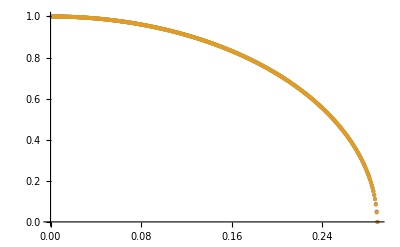

```mathematica
ListPlot[{listdatacomp,listdatainc},PlotRange->Full]
```

```mathematica
listdatainc
```

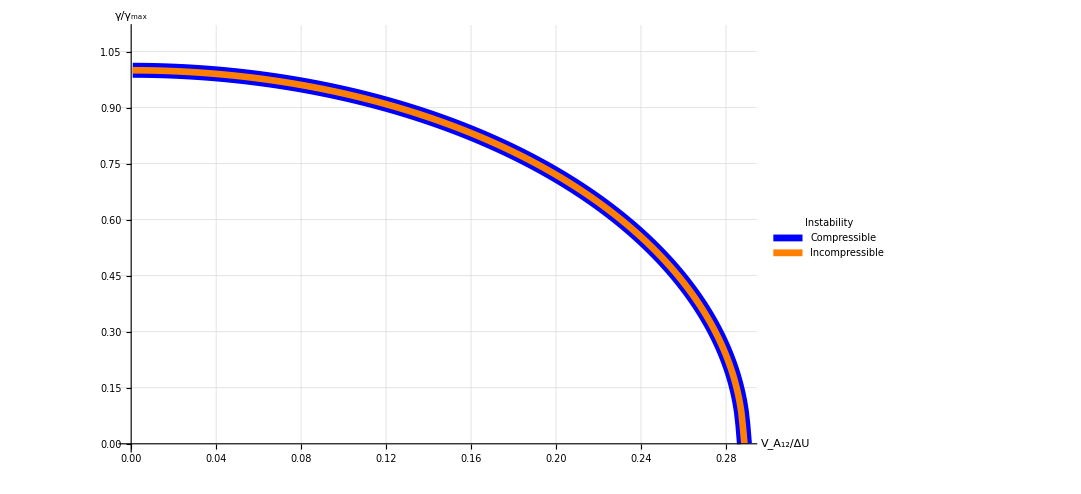

```mathematica
khcompplot = ListPlot[{listdatacomp,listdatainc},
Ticks->Automatic,
Joined->True,
PlotStyle->{{Blue,Thickness[0.0135]},{Orange,Thickness[0.006]}},
PlotLegends->Placed[SwatchLegend[{Style["Compressible",Bold,26],Style["Incompressible",Bold,26]},LegendLabel->Style["Instability","Title",32,Bold,Black],LegendMarkerSize->20,LegendMarkers->"Bubble",LegendFunction->"Panel"],{{0.5,0.45},{0.435,0.85}}],
AxesStyle->Directive[24,Bold,Thick],
AxesLabel->{Style[Subscript[V, Subscript[A, 12]]/ΔU,Large,Bold,Blue],Style[γ/Subscript[γ, max],Large,Bold,Blue]},
GridLinesStyle->Directive[Blue,Dashed],
GridLines->Automatic,
PlotRange->{Automatic,{0,1.1}},
ImageSize->800]
```

```mathematica
Export["KH_comp_compare_low_Mc.eps",khcompplot,"EPS"]
```

KH_comp_compare_low_Mc.eps

#### Scan of Mc with vaying magnetic field strength

```mathematica
kx=1;
ky=0;
g=10;
U1 = 15000;
c1=20000;
c2=87178;
```

```mathematica
N[Solve[200==ρ1*20000^2]]
```

{{ρ1→5.×10^-7}}

```mathematica
N[Solve[200==ρ2*87178^2]]
```

{{ρ2→2.63158×10^-8}}

```mathematica
d2range =Range[0,240000,1000];
```

```mathematica
a2 =ParallelTable[NSolve[-1/c1^2+1/c2^2+((ⅈ kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(ⅈ kx U1+γ)^2))+((ⅈ kx (d+U1)+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(ⅈ kx (d+U1)+γ)^2))==0],{d,d2range}];
```

```mathematica
khroot2 = Flatten[Append[a2[[1;;152,1]],a2[[153;;All,3]]]];
rtroot2=  Flatten[Append[a2[[109;;152,3]],a2[[153;;All,1]]]];
dvals2 = Table[d/(c1+c2),{d,d2range}];
khrootdata2=khroot2[[All,2]];
rtrootdata2 = rtroot2[[All,2]];
normkhdata = Rescale[Abs[Re[khrootdata2]]];
normrtdata = Rescale[Abs[Re[rtrootdata2]]];
data5=Thread[{dvals2,normkhdata}];
khdata=Thread[{dvals2,Abs[Re[khrootdata2]]}];
data7 = Thread[{dvals2[[109;;All]],normrtdata}];
```

```mathematica
ClearAll[kx,ky,g,U1,c1,c2]
```

```mathematica
khroot2[[241,2]]
```

0.000102844-36817.3 ⅈ

```mathematica
d2range[[241]]
```

240000

```mathematica
Length[khroot2]
```

241

```mathematica
compnob=FindRoot[SetPrecision[disprelnog[SetPrecision[3*10^-7,wp],SetPrecision[8*10^-8,wp],SetPrecision[200,wp],SetPrecision[0,wp],SetPrecision[0,wp],SetPrecision[10,wp],SetPrecision[1,wp],SetPrecision[0,wp]],wp]==0,{γ,test},WorkingPrecision->wp,AccuracyGoal->150,PrecisionGoal->150,MaxIterations->20000];
```

```mathematica
wp=850;
μ=SetPrecision[4*π*10^-7,wp];
list = {};
Do[

Do[
test =SetPrecision[khroot2[[index,2]],wp];
B1=B*10;
B2 =B1*10;
B3 =B2*1.2;
B4 = B*10000;
result0 =FindRoot[SetPrecision[disprel[SetPrecision[ρ1,wp],SetPrecision[ρ2,wp],SetPrecision[P,wp],SetPrecision[U1,wp],SetPrecision[d2range[[index]]+U1,wp],SetPrecision[g,wp],SetPrecision[kx,wp],SetPrecision[ky,wp],SetPrecision[B,wp],μ],wp]==0,{γ,test},WorkingPrecision->wp,AccuracyGoal->150,PrecisionGoal->150,MaxIterations->5000];
test1=result0[[1,2]];
result1 =FindRoot[SetPrecision[disprel[SetPrecision[ρ1,wp],SetPrecision[ρ2,wp],SetPrecision[P,wp],SetPrecision[U1,wp],SetPrecision[d2range[[index]]+U1,wp],SetPrecision[g,wp],SetPrecision[kx,wp],SetPrecision[ky,wp],SetPrecision[B1,wp],μ],wp]==0,{γ,test1},WorkingPrecision->wp,AccuracyGoal->150,PrecisionGoal->150,MaxIterations->5000];
test2=result1[[1,2]];
result2 =FindRoot[SetPrecision[disprel[SetPrecision[ρ1,wp],SetPrecision[ρ2,wp],SetPrecision[P,wp],SetPrecision[U1,wp],SetPrecision[d2range[[index]]+U1,wp],SetPrecision[g,wp],SetPrecision[kx,wp],SetPrecision[ky,wp],SetPrecision[B2,wp],μ],wp]==0,{γ,test2},WorkingPrecision->wp,AccuracyGoal->150,PrecisionGoal->150,MaxIterations->5000];
test3=result2[[1,2]];
result3 =FindRoot[SetPrecision[disprel[SetPrecision[ρ1,wp],SetPrecision[ρ2,wp],SetPrecision[P,wp],SetPrecision[U1,wp],SetPrecision[d2range[[index]]+U1,wp],SetPrecision[g,wp],SetPrecision[kx,wp],SetPrecision[ky,wp],SetPrecision[B3,wp],μ],wp]==0,{γ,test3},WorkingPrecision->wp,AccuracyGoal->150,PrecisionGoal->150,MaxIterations->5000];
test4=result3[[1,2]];
AppendTo[list,{ρ1,ρ2,P,N[√(P/ρ1)],N[√(P/ρ2)],U1,d2range[[index]],N[d2range[[index]]/(√(P/ρ1)+√(P/ρ2))],g,kx,ky,B,(2*P*μ)/B^2,Re[result[[1,2]]],Im[result[[1,2]]],N[B/(√(μ*(ρ1+ρ2)))],Re[test],Im[test],Re[test1],Im[test1],Re[test2],Im[test2],Re[test3],Im[test3],Re[test4],Im[test4]}];
If[Mod[index,10]==0,Print[index]],
{index,-1,-241,-1}
 ],
{kx,1,1,1},
{ky,0,0,1},
{g,10,10,10},
{B,0.00001,0.00001,1},
{U1,15000,15000,10000},
{P,200,200,10},
{ρ2,N[200/87178^2],N[200/87178^2],1*10^-8},
{ρ1,5*10^-7,5*10^-7,1*10^-7}]
```

-10

-20

-30

-40

-50

-60

-70

-80

-90

-100

-110

-120

-130

-140

-150

-160

-170

-180

-190

-200

-210

-220

-230

-240

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 850. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Length[list]
```

151

```mathematica
ρ1==1,ρ2==2,P==3,N[√(P/ρ1)]==4,N[√(P/ρ2)]==5,U1==6,d==7,N[d/(√(P/ρ1)+√(P/ρ2))]==8,g==9,kx==10,ky==11,B==12,(2*P*μ)/B^2==13,Re[result[[1,2]]]==14,Im[result[[1,2]]]==15,N[B/(√(μ*(ρ1+ρ2)))]==16,Re[test]==17,Im[test]==18,Re[test1]==19,Im[test1]==20,Re[test2]==21,Im[test2]==22,Re[test3]==23,Im[test3]==24,Re[test4]==25, Im[test4]==26
```

```mathematica
listmc = list[[;;,8]];
listnob =Abs[ list[[;;,17]]];
listb = Abs[list[[;;,19]]];
listb1 = Abs[list[[;;,21]]];
listb2 = Abs[list[[;;,23]]];
listb3 = Abs[list[[;;,25]]];
listgamc = Rescale[Abs[list[[;;,14]]]];
listgami = Rescale[list[[;;,17]]];
listdatacomp = Thread[{listmc,listnob}];
listdatab= Thread[{listmc,listb}];
listdatab1= Thread[{listmc,listb1}];
listdatab2= Thread[{listmc,listb2}];
listdatab3= Thread[{listmc,listb3}];
```

```mathematica
listabsdiff= {};
Do[AppendTo[listabsdiff ,Abs[listnob[[index]]-listb3[[index]]]/listnob[[index]]*100],{index,1,241}]
```

```mathematica
listdatabdiffplot= Thread[{listmc,listabsdiff}];
```

```mathematica
list[[1,16]]*1000/(list[[-1,7]])
```

0.0204937

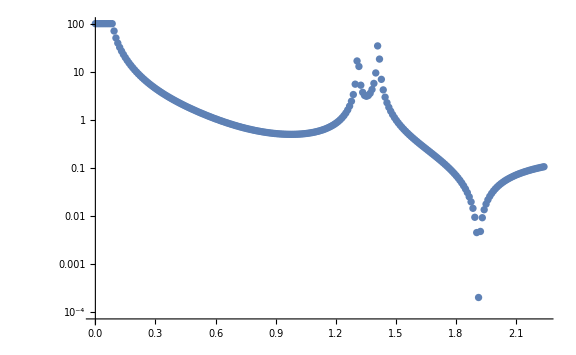

```mathematica
ListLogPlot[listdatabdiffplot,PlotRange->All,ImageSize->Large]
```

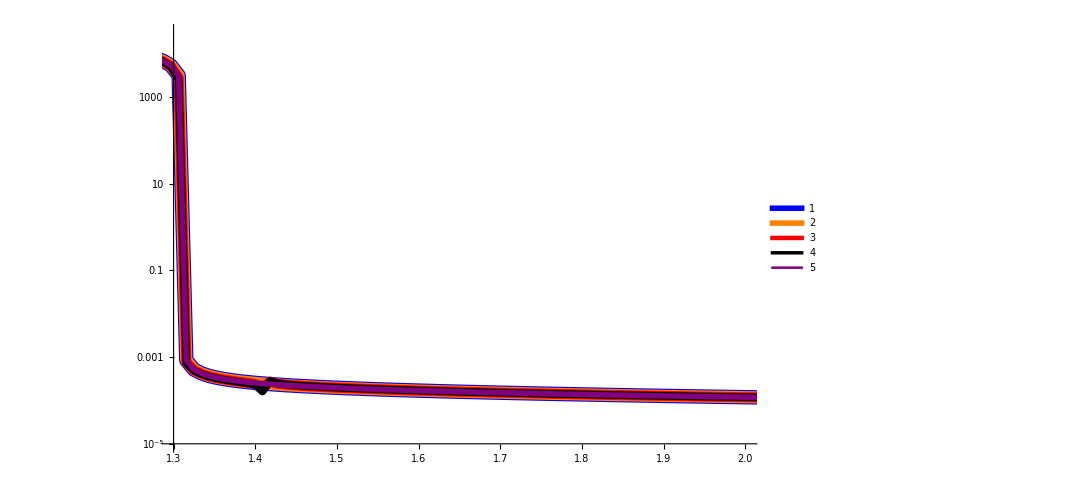

```mathematica
ListLogPlot[{listdatab,listdatab1,listdatab2,listdatab3,khdata},
Joined->True,
PlotStyle->{{Blue,Thickness[0.013]},{Orange,Thickness[0.011]},{Red,Thickness[0.009]},{Black,Thickness[0.007]},{Purple,Thickness[0.005]}},
PlotLegends->Automatic,
PlotRange->{{1.3,2},{10^-5,3*10^4}},
ImageSize->800]
```

```mathematica
N[180000/(√(200/(3*10^-7))+√(200/(8*10^-8)))]
```

2.37405

#### Plot General results

```mathematica
listb=list[[;;,12]];
listgamre =Abs[list[[;;,14]]];
listgamim = list[[;;,15]];
listdatatestre = Thread[{listb,listgamre}];
listdatatestim=Thread[{listb,listgamim}];
```

```mathematica
ListPlot[listdatatestim,ImageSize->Large,PlotRange->All]
```

```mathematica
ListPlot[listdatatestre,ImageSize->Large,PlotRange->All]
```

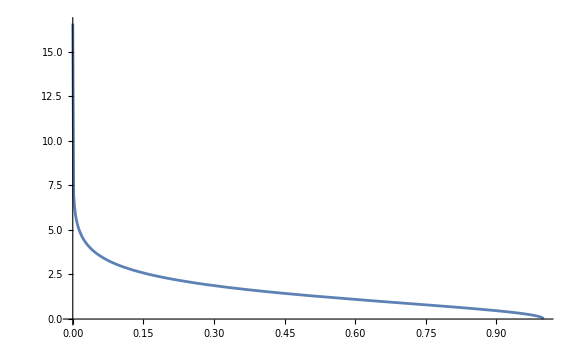

```mathematica
Plot[ArcSech[x],{x,0,2π},PlotRange->All,ImageSize->Large]
```

```mathematica
wp=200;
μ=SetPrecision[4*π*10^-7,wp];
list = {};
Do[
exitvalue = 1;
test = SetPrecision[khapprox [SetPrecision[g,wp],SetPrecision[√(P/ρ1),wp],SetPrecision[ √(P/ρ2),wp],SetPrecision[d,wp],SetPrecision[kx,wp],SetPrecision[U1,wp]],wp];
Do[
If[exitvalue<1*10^-20,Break[]];
result =FindRoot[SetPrecision[disprel[SetPrecision[ρ1,wp],SetPrecision[ρ2,wp],SetPrecision[P,wp],SetPrecision[U1,wp],SetPrecision[d+U1,wp],SetPrecision[g,wp],SetPrecision[kx,wp],SetPrecision[ky,wp],SetPrecision[B,wp],μ],wp]==0,{γ,test},WorkingPrecision->wp,AccuracyGoal->64,PrecisionGoal->64,MaxIterations->10000];
AppendTo[list,{ρ1,ρ2,P,N[√(P/ρ1)],N[√(P/ρ2)],U1,d,N[d/(√(P/ρ1)+√(P/ρ2))],g,kx,ky,B,(2*P*μ)/B^2,Abs[Re[result[[1,2]]]],Im[result[[1,2]]]}];
test = Abs[Re[result[[1,2]]]]+Im[result[[1,2]]]*I;
exitvalue=Abs[Re[result[[1,2]]]],
{B,0.00001,2,0.00005}
 ];
Print["One itteration done"],
{kx,1,1,2},
{ky,0,0,1},
{g,10,10,10},
{d,500000,500000,10000},
{U1,10000,10000,10000},
{P,300,300,100},
{ρ2,1*10^-8,1*10^-8,1*10^-8},
{ρ1,2*10^-7,2*10^-7,1*10^-7}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

One itteration done

```mathematica
Export["disp_b_test.csv",list,"CSV"];
```

```mathematica
Save["disp_b_all_parameters_data.m",list];
Export["disp_b_all_parameters_data.csv",list,"CSV"];
```

```mathematica
test = SetPrecision[khapprox [g,c1,c2,d,kx,U1],wp];
result=0;
increment=0;
list = {};
listbeta = {};
Do[result = FindRoot[SetPrecision[disprel[ρ1,ρ2,P,U1,d+U1,g,kx,ky,B+increment,μ],wp]==0,{γ,test},WorkingPrecision->wp,AccuracyGoal->64,PrecisionGoal->64,MaxIterations->10000];AppendTo[list,{(B+increment),result[[1,2]]}];
AppendTo[listbeta,{(P*2*μ)/(B+increment)^2,result[[1,2]]}];
test=result[[1,2]],
{increment,0,0.1505,0.00005}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

Trying to fix all but one variable and see if this is good enough for fitting

```mathematica
wp=350;
μ=SetPrecision[4*π*10^-7,wp];
test = SetPrecision[2.446558487830698798365095916203703752347528183760559575177293370675541545604193452944360508306203038669377989809535101903099491178284009139586855706085071186057208726817761063404846456848782007012813821236443041246259246459927183355153457338554518055527670541179482`250.*^-6-25681.567340769844629027621958898738758299457927230281771415459992078827761875938493774266750466569434125942139557202173966861954986490820132072403488900510545991777940100620882588508832712741836138880749626685169152522919842295671110378864887380642635101754414772821103866561`250. ⅈ,wp];
list = {};
Do[
result =FindRoot[SetPrecision[disprel[SetPrecision[ρ1,wp],SetPrecision[ρ2,wp],SetPrecision[P,wp],SetPrecision[U1,wp],SetPrecision[d+U1,wp],SetPrecision[g,wp],SetPrecision[kx,wp],SetPrecision[ky,wp],SetPrecision[0.1,wp],μ],wp]==0,{γ,test},WorkingPrecision->wp,AccuracyGoal->64,PrecisionGoal->64,MaxIterations->50000];
AppendTo[list,{ρ1,ρ2,P,N[√(P/ρ1)],N[√(P/ρ2)],U1,d,N[d/(√(P/ρ1)+√(P/ρ2))],g,kx,ky,0.1,(2*P*μ)/(0.1)^2,Abs[Re[result[[1,2]]]],Im[result[[1,2]]]}];
test = Abs[Re[result[[1,2]]]]+Im[result[[1,2]]]*I,
{kx,1,1,0.01},
{ky,0,0,1},
{g,10,10,1},
{d,400000,800000,1000},
{U1,0,0,10000},
{P,200,200,100},
{ρ2,8*10^-8,8*10^-8,1*10^-8},
{ρ1,3*10^-7,3*10^-7,1*10^-7}]
```

```mathematica
list
```

{{3/10000000,1/12500000,200,25819.9,50000.,0,500000,6.59458,10,1.,0,0.1,0.0502655,2.4448300240161705056270529869010201678540367579301528219700605390144309706858432213613318925477099649634124357967235260116120993132459561373880839436249606633369061806265389725637549872604845276174766503332449198942997324531668689210007269822236559028294421732816345418973999003352486477655655111923150542314629328088040614993621516780774026342679845×10^-6,-25681.561759857029627323453266375991746861234202199054033740003157047191518709389223408617993616634738323811321504109395380928581678781488369370866476029158946803473268527658119906731292580184057656869373792483147447546174749788742442555964021260722221778656443337455906096057812754742227867096030068114617988690717206368106264038664700407205439600612},{3/10000000,1/12500000,200,25819.9,50000.,0,501000,6.60776,10,1.,0,0.1,0.0502655,2.4435050266820712186972871126219158913392201291249303612711034606155083536685859178945435742041260897214173683180505969086948300482991141630590163915299680136732515944250813313547512094168407297285180540327801047237422854261868155149244248286975104317183539002063522947693372959276732709963813364417396614866276812589493075663567063828613199916962271×10^-6,-25682.150923958173466812343777548846476854325348031028887292246955343245743088570856124828083721715007009925043587337706760700049247592319253523513045995741598142927675580408596803052349043363288835618457842319136920217281325193548692671326945114332998056385632166147488480152821132507146525999535064659698639752398358502374129859932718702386922023875},{3/10000000,1/12500000,200,25819.9,50000.,0,502000,6.62095,10,1.,0,0.1,0.0502655,2.4421542108407436656650101589936584104006652022116576350145256869462684530217229437744646730770303848373191320345526179611531691555039618027901576947314784027942810344059083391523325135766593814453207006567447294221343404315804529966170791168084482277315615221704112772994469148219118239713458523311773275938747977563243025561545867058110497789050285×10^-6,-25682.736317113020701782505056475983407715722159460875426594826292355043427460689766662317758156781396260285021137940738315835362692600746037100085201237548850610067749995717719697602043793649502542830474537047841115555311800808422950165653331184855469131208043550751256560078854781810110215123312019728646988675392831648075555916745833750203718560973},{3/10000000,1/12500000,200,25819.9,50000.,0,503000,6.63414,10,1.,0,0.1,0.0502655,2.4407781118935077011558138543737648225084368171804904732755378815204962735945454822151633702299505748780880920764836412882886153210659687531783052782706192818655555440973141162023728586616347295189000980638453872318764225767520484768939391781151437117585975466324118179795020898678984428411060888187334245468050532280308161726473725285569573085066248×10^-6,-25683.317971554840793911936017818152025016401421482407663863581766198568251203116826179563307777001429691975368406401605523032093378497345357161395144104684353375556295527789517478372376287861868188320913476315612137868576839427347647650243708863704669408525889769926844714817851071652337458349475453630773782284989028170389561616202200822288227620293},{3/10000000,1/12500000,200,25819.9,50000.,0,504000,6.64733,10,1.,0,0.1,0.0502655,2.4393772547328519116861671792239752673245947160224883171373477717077073957015019077031849170582904363888776091978942878903099010309699595790238598853357669567818705186054160893161234611787528324005737397696601162299043524872666493817472156245710653219047980201920844208379953175255145360890141511448108607714970418442969131719612394414798723010007627×10^-6,-25683.895919172020440713543817621210765820572664681437222930079215348214753190920156103646061401574855631208528279115012517415525905444919694025786629211232178372511261956941560845281535005116424385315078501915018139398240914437878474727376049170896731511703879592225011851979487219467081462719297693267151914973312048077842606933455828909781330933962},{3/10000000,1/12500000,200,25819.9,50000.,0,505000,6.66052,10,1.,0,0.1,0.0502655,2.4379521539789131753416301543154516236269377554979502997901913640653970469395499895758698164479503131846580807523867074830567847409641702058795030319925443384207023891095737771910937193472660986912031222023797241151605613910579818379536012270882214104111495771049834697042986251617370729836868573514819753648924120970626787693585486600272003261855685×10^-6,-25684.470191512496815813107635624337090647244932508610538828176788818360154916093771862518959030883581455366354652899015010987617936390820304711306225936523478188055955077488282105817046489375086480687997186618956315147963368936117542225239710679022871664444258966723705520990708045107500404416236593760146506348216681848687338762030749534344837296082},{3/10000000,1/12500000,200,25819.9,50000.,0,506000,6.67371,10,1.,0,0.1,0.0502655,2.4365033142096546654759749851395716335383104154829298112655975823256138634485176451784980119237020990704572993926883894342513950097140287704898963140488375605934032475760958762241690960292778808109130371116902756830447342904788476918385131005029507818200822664194414080962675309869410223830851284183067831803424440721421582799241807601074946508719299×10^-6,-25685.040819788124264237005835746437564055132060464719510856036882693042050507278228171453078622891438440549748829079443604563429351599260663143639392546068465545181909321160518832222923086617796098999220573142658094422657003197631057230530824515935782418429445141797782285718912908878192849373616104137211887296138717886776691469601816421916924759683},{3/10000000,1/12500000,200,25819.9,50000.,0,507000,6.6869,10,1.,0,0.1,0.0502655,2.4350312301849412787967069618651415326128946402056472703663476720591150300286070859902354411841084691232575290611603404991187194713212761341468455863080630313451729145889651044264039416317394585646761388276908605572089985392806854974458866831821486260020905446704225837523635836440799941626066992331126099761220030799742089043255365995254042905606488×10^-6,-25685.6078348789755950465976758202551969935282362854704023574186094658703714607863585625651627153593731706698736647989178037628402603250476549910291954666668124662831100386879378572688772824977765603364050833688953714579586159785288050321600063479180115137983917201138645342973433635295906407591298861591233333454406772798518871548186688667942923393},{3/10000000,1/12500000,200,25819.9,50000.,0,508000,6.70009,10,1.,0,0.1,0.0502655,2.4335363870647041008031801094658400905529884558510731694140750999306778557649513694102908521459761450594539203420818367051177026448559072596719934151366259326997730985358727751873607707772387000863097549653144652944768528058008119684507743725237176069635126460726798318758206368931719399315843842899967928637578194305131004975928134440252846852426294×10^-6,-25686.171267337579091585561544015041808574072964617241212952473890817920295572989221912769278865213148300427352883307734286495307265207486734734908975173248097827136008409353361061576055210822410986833505056555270676326830464189252512269853215184441737581871687920059082787650340138113370299768363714557273473809407610892045062524748467056755485162626},{3/10000000,1/12500000,200,25819.9,50000.,0,509000,6.71328,10,1.,0,0.1,0.0502655,2.4320192606213784692414695279657283575599194280685577902157140760771505755783431334660594429194470028240008268225205974665657978252804615563614656256996353211596108573451848342557635125416832997295928022824895415369854810631978090442819563508115824348135100137671649112130586326579745121620310060133815161788574931145653633401926629466833551954766534×10^-6,-25686.731147393092338009791223248657042472960651193396547103145171845063490846739042874155343742193969434156908530749885009213387288926258673409285697794577243983601077364817239719940918332233949492980683300491208991968967696431117617900540697499726350353421053395422585754953270900150879589117879416227731177160929863635534183402161878604300582399365},{3/10000000,1/12500000,200,25819.9,50000.,0,510000,6.72647,10,1.,0,0.1,0.0502655,2.4304803174467934437140419140097170923879523386117888653848910702220753821053137032273104637768523880469118115160244137643851097186059378423223954661156998122918755020310952818664515925042372949173998008211073018790758060550707214640864336182372179209273615488509650064084870359915198457311866173979423375441987971827001829118234026835807307025828823×10^-6,-25687.287504955413939635447720659380301930635367706075638833955691389345739628619207513671054148538323931835433629234870788296534874345171363679691595165263616372568949129063309004331883769020128678040080095642002315877839075933934986665273960745161671730460069888601345806158935502634394979053449578194983852476446426301137433090034133332623500069247},{3/10000000,1/12500000,200,25819.9,50000.,0,511000,6.73966,10,1.,0,0.1,0.0502655,2.4289200151536840223452633581284286651762015147538738719483749519899538720564286979435620215671689640248753894713980605242727152189695780197035626405704131828510656137141625610499879234031369205079119766499969585551113686133287010848727883040884282047651003437501356298733377139394820314999475675858964333848656921712466763506975488264526411375664222×10^-6,-25687.840369619234193958552831197970505588288971000663133548970520767631727124779829149364715308580835536577524714993928743990163468896337464346371767998879897539519998706296498746977969331098288705182673788733831215972301455838012850243556217684292699604366943639428666813362629065180221484779277425020386062319390951426969553349622058687393649115902},{3/10000000,1/12500000,200,25819.9,50000.,0,512000,6.75285,10,1.,0,0.1,0.0502655,2.4273388025719912507533851641809641904453880616911559311619714355685427392499340052574685887312202703030033068687632165691230781236541046567136816927504705098687957855108155526347764383490079328783135527545111264533241810317104169016816767289247519134943941241247163415864428583955620327140322735494720889695338980433468564421396801189734020551246502×10^-6,-25688.389770668025748958468166074194356151738638328589828858546301546007643985254118004461088583418062466080168249500630302759376223956179545877137403079462799039519665783573910575991871772844257062265425827263661526269665939675522571744967800050668702280522394728897275892173318236348640851805023262358548475689432533010361401802381019106717208426264},{3/10000000,1/12500000,200,25819.9,50000.,0,513000,6.76603,10,1.,0,0.1,0.0502655,2.4257371199401094315506582582418908995111426944767640542120213408598590827542704060836686179938610329092698432800942490506632743038182928051435087166537572795114801410405640796739173945571438286198374921765007788446192859230860858591800872627336661295281934235556243043857642827929687811238297610395799903396138435568707842931034870476385257600799331×10^-6,-25688.935737077975265487378651373092774270399770555123066142491078525683100720297796606097066001774530767591695180649625073058603827199282709243661601307226696450251152937314380612207440746452781263628166720538070494705619393725337612464878007854180090619231770911769197098589497122825170780626110290763687815021025563455498095896237714099708720484487},{3/10000000,1/12500000,200,25819.9,50000.,0,514000,6.77922,10,1.,0,0.1,0.0502655,2.424115399091233951913881819709100908407810613846737305143479210040726820585415914864845013548856737684589596855883225596619279113025656650149683919182659118630823183536535071778757006999718540433891084528529117750099490030544800058589404553948425607863752606397163015746369088243723989479101787778849371939007766684731336943010176278649651602569603×10^-6,-25689.478297521857081158406156834650943163349894235535940824291851102460623090944993704966713054162302312598850951039551986235568084708300622287201222471975570970755566447417722697787501535937476498129501423769419208823044593465412487496447071033263433534380729445447305322344661254598748711747415627536975431023900354324989119581493381051091755968886},{3/10000000,1/12500000,200,25819.9,50000.,0,515000,6.79241,10,1.,0,0.1,0.0502655,2.4224740636349577908186354962797593135871955029620579587566039045487399936860147878861640806373847270562319062115863994248411655263518267971590848532508697004185781164424151916403005566808694582734454324528835210757188568692734339511969947581705089177722378947683789310563165517470129578026941572424392210398847824720526210742881229744227534623908472×10^-6,-25690.017480372849854166388161032402539292299114038123516873094316227350688651617984658978400021668664381608257340928083104288189172871039489694372471309583435173511101162146089655507710041735181437328529985837984991939236715765729189555218767694210152224235156232246082326241246329166621052464462867787168693190226996067788511412376612043235371015524},{3/10000000,1/12500000,200,25819.9,50000.,0,516000,6.8056,10,1.,0,0.1,0.0502655,2.4208135291342595353063566838479196339109624172121650749339660913928248509322168745898397358048117406978669421212972590877754531040820745932918072312566131437178657951844983365535764158535235823669934454828084271142580215518753412582510281314570305788673796091418353910445010619072762947832172184304798626970476333509178950727922844882242150574119902×10^-6,-25690.553313708297146898089831916043610410681731909878540531247205871260720794830408694460989319645450084217414578451950615839838075621634429906693487440715593645675979099552016961315008178672901851611494201679368608026054848431528573138532057388435895894628891113856511840585842042192010331558487636396465416560074636771603477616076163867842474051233},{3/10000000,1/12500000,200,25819.9,50000.,0,517000,6.81879,10,1.,0,0.1,0.0502655,2.4191342032780207162271208370580419719906741470348040617597580000480254731158280111635561908424883999100541129766783345139816950979039015729000472286309154408558749291776836260536547123717940367084342902109841452355037685620102371115223839793581370921763135970752271275357561947122660147968992313561274347209897080032746041793630470112181826460412928×10^-6,-25691.085825313412891003340750349575086022296311630105497542000556904961283698235944752350920813051607752736235366439609361157145075551917106995100690412719579705767421720563075969911315495402964524818916462153828006908283914373189247214448399403004500687526539371086046039370984436949040370333227965567961833735071433703540099882401773515257678789423},{3/10000000,1/12500000,200,25819.9,50000.,0,518000,6.83198,10,1.,0,0.1,0.0502655,2.4174364860492054583898132689441870112928299760675616648561574727389671477265884252733888099554297179116434280688899346846326422880839122090490720509435455389420692632958063789357365435674452684655854611653043585616815727263189981778686153315049775316797118369043921906979398968719578059072444156802596863657207678322962130635412224081597988401289015×10^-6,-25691.615042684932657796201689056711028647188996291138865508060163233840665447586876863667133977115804985214688407041070116779520719634396814363956021934766974611817793267068068060598024985427560604573228455935942063589158004733849473581850430030474167863322523939533952094906758499665773218554204734340925044986060113733457359116346075212982854424312},{3/10000000,1/12500000,200,25819.9,50000.,0,519000,6.84517,10,1.,0,0.1,0.0502655,2.4157207698888308185857640921733374248891200979700283964915553077077917653632142888872190811859513087471584449594836769287182840783259232165034820427681243611130581144034663162178990272657510844096098393235634480518594261121249618972837690453681017823970616402952827452919369419560526958790066099545410079176483124492853372959449178222584422096875045×10^-6,-25692.140993034711640426904646002023762108388348234507921230070126483708442393174151388557616701867736144742043359988235268843029105025266113946389704252174580503481356733504525563172560431215638844800403338766779098460329704163672745780074033947048853832801264032634120980791324653432529780922895409370568967398745857732586337475689140532231869192764},{3/10000000,1/12500000,200,25819.9,50000.,0,520000,6.85836,10,1.,0,0.1,0.0502655,2.4139874398558517486458673477624311273399587748064335670741402639199959945159551793788914584534198415116955285569021927373268362366256507465979918607945937036215308160181921389404687499791302672591536780309466093351995206259729309616991826510052067738649505944842000747045918500285644550063966817644533479961884574528460243274517105472503580063373644×10^-6,-25692.663703293270237202326978092577373258200453307218324585864083183855494528730284734671975546424318234883463869789282317180728337210504787471555016830401047076609218054506867164869741721677682849291684190721634495643650681058394251326679084281411288359051764859383441847055938283093503916714397293355469756647098292662553587627334914578887287912136},{3/10000000,1/12500000,200,25819.9,50000.,0,521000,6.87155,10,1.,0,0.1,0.0502655,2.412236873783080361114708769766560780984760438648254404040915462377161009470751856432510516776228424692520145549484249697133152018627747180551610448875763984313064575686289497790256074256074319029477095136493250840088530893519695530773142494940489022992856756531829528593819423117044809987128635958486979678798452727313292760210368201683600422328745×10^-6,-25693.183200113288108726732112628130339967432522412585748775083499304775893658551706656459595524237995406546216180468250180537481516048079710545417898051115269355631085752752337628686203418011953037818265220977416937777903686595081065905781543469076216304635092293753115738835397866367379056929498488523268726633177144543716360154806116442706313055232},{3/10000000,1/12500000,200,25819.9,50000.,0,522000,6.88474,10,1.,0,0.1,0.0502655,2.4104694424292550842783529127709102786071299050813661968569401652785127767850095492312173765118409710500870183595741565862922618802261792775659876426195439238166364248646932094942130235255899139370735092073336533501990464897508289140113816441289469648187443837533479296164067142861408968371833538498058122244452163467907182909038204686514338583528296×10^-6,-25693.69950987304756517722097436307981642817945925122310122869357723973091966016947121968359763518931559095308293311618846527836713512313237756863508673328773721492106822193649892090353425994514911119834298089510702953682056315610202233407749194090669790046869929924350357420937920662398179663461485845885518413860865185642483279508602277204618923303},{3/10000000,1/12500000,200,25819.9,50000.,0,523000,6.89793,10,1.,0,0.1,0.0502655,2.4086855096273713635710562105266942136335108047801038520407676654692965256466694215872278531970855557260344550467149049161105424554160877808041581857179463329046074395352238596699229621712794672301130282989886596483215889697271526966609783292335759704708407895681772968777335812224136480023759744572032922423239382557434285480686531368547556411684206×10^-6,-25694.212658679827124011782147710098220733575269668011120894059285559895202359279831106101736399934657920548742523441542389097871855751074877584949606899647720586061999601014904805793565319546175959264959474158604922713624566339003228641959142031646682519840426940737833471752484776525570892782955382818028585104310354615662034426478056063961764078975},{3/10000000,1/12500000,200,25819.9,50000.,0,524000,6.91112,10,1.,0,0.1,0.0502655,2.4068854324293817905991605848989441613423586227759892552355295723681742660235801830332300691103599734052577140655871407097724196465556569049889390041408834223815792121197550268852524714618517997016380007850338979934742628185932429378744791349582374793461191135755392887417181329878186545089340699382346676108646756907759309426045712634450167848246269×10^-6,-25694.722672373246062724197634539815024864063777230888027294140421693360583756442738571728765286446491473816417122827239890239816111157470674807701152214215320267582267732094367223342379724564177808557866495150419954541326347118345890444703243627087166542169840218599542731054705574658398880886294513179019408312363072853851790383292730305985000464956},{3/10000000,1/12500000,200,25819.9,50000.,0,525000,6.9243,10,1.,0,0.1,0.0502655,2.405069561247369912308299850958521479305336662609465569877176229230044058231988668556590119546600870748553630635448229649712975155578163264422374554888520308929335723171963120729284789509684064381520035357490613237905124942865794104951898776454371643965575600501814709113012218940553205356070265210877948548892941507596661268574642659575553657670784×10^-6,-25695.229576528560775901742713340067428810828958718568335126759289667858065756641323295034617377263870757186175231097190685045380760654442329486072527802094480037874482004079267123084341089312035564852886102007195638741291373270345028125687719121226319649646236211999660327113804057156049133813870520521825924999108624792761976982356131663429899398743},{3/10000000,1/12500000,200,25819.9,50000.,0,526000,6.93749,10,1.,0,0.1,0.0502655,2.4032382399912984846748963737822381743781389931955162575316687834604262962839748512479772753048016262054875913082657536799009477266358855903060383513638593709924703187787150045320099715766630349053611236392393773516443651587330476835123575574951286852470914696064500109807674226938633834426761599404927019675727255455950638961215254119481064037922273×10^-6,-25695.733396459913730801190527569194664666006074376566515307680093713081771885484401120262521772546225264797339341127557835117870926646492053593026523969636810639346669604678707423285426052613203833322722838297733889336500756944279874229651664731745774952671534954271788426340061696286268645332564608474898497007974141862080271317037309063215658996968},{3/10000000,1/12500000,200,25819.9,50000.,0,527000,6.95068,10,1.,0,0.1,0.0502655,2.401391806203429581539523206707549847327666524201712785349728146849069761298200403619994660657438798367385125589238447496173929007631661900081751302951635432801388975357179119853628574383960682088826606973808746580810446118218914493435853058987835435064717539254233509818270884321887702145803291490734450526879217747120619678905009458950657694592298×10^-6,-25696.234157223535800928857003419866619256246755641483715935657993096042922766784737133113405630726724119804657819185046778237018583146297514928854446924692837300406384453162596152555841494993934467773139520807373906304592704900736903000136810446160087169655923525819663007480687482198085188199214028340933961831709964798187871301250938637890756100538},{3/10000000,1/12500000,200,25819.9,50000.,0,528000,6.96387,10,1.,0,0.1,0.0502655,2.3995305911895107439378354384713180498682442529154362371945865751129295839113201882453033751205434553971370385037182414636190159871586416208988104802802265568240859869690154104053485498188782503502976711396032460406289121526913428111442734454397535473087996156964902890992895783814213633786716071111909617744445357468164158810241933573581426269953786×10^-6,-25696.731883620902742684241617526137455620298272919202989304611965036210737623507928011945369246847234958558938268342333075628862990008829133045565350940094704541191993025903933860610416134369497367431195931260374615266254381640013788504471077182560391011704534591888623995170001142656880233904644794002500488119737526308282176329669587076795702728096},{3/10000000,1/12500000,200,25819.9,50000.,0,529000,6.97706,10,1.,0,0.1,0.0502655,2.3976549201468182529325562927579000307628961582276450316080938052532292305907047090305967660148965151086661014267512659557705561034072884323455726492028592642832604701420150264445855519102241275474534360856491188139946938637655783724904040790478063840990851492501202700091929180870484414827677909691334144802565744271517515656238863773551459326641694×10^-6,-25697.22660020184656599735139233918242151086734454007177650305152839260271644534991003363444217288734439838423528010689601866697971310032829524699954709207302958508359384434046022118788417817226692552421765807858482197590701916495210632527802049588752133318033903481540971038049597265220351881795799679271741537327566947409119501087370662458400325224},{3/10000000,1/12500000,200,25819.9,50000.,0,530000,6.99025,10,1.,0,0.1,0.0502655,2.3957651122891456241882524779527507367993038033697976256631913925105750356386814088980992064781577140817618080767445442012106940602151905278288657933703916252962560738039783162060252043774161472785365930932162158936266580027062635106966766215953326012791344559961189725050659632030971949662943031816112596670478587745196108916090219750518437173829454×10^-6,-25697.718331267622536050326478335851428343043016339805055437080612283493845284780144456756844336882931733097891521225295718158452599840768517745805525321959288113786807005238022129962759857297842617902715727945748232957723169839353271659483064828025658691644069885322965524435283606508007604050479644191653504848435706981343188614455321337523072071465},{3/10000000,1/12500000,200,25819.9,50000.,0,531000,7.00344,10,1.,0,0.1,0.0502655,2.3938614809688225502981321085430745588878270772626283859581244634272688646578646803244942021681274412470142946604105652426993927891857577438609487658501504071316788930223995830353604384544884547111488814800263299192942946287534199977794053060057231778617712800982119086717061992729573106053660629807815130649017596443433468759978561497167299623821708×10^-6,-25698.207100873932529617968616341679563204202295315616489795155064829369622938982138369976473753762514360797183637678397437385019260059351468998932055706387797002787538112015625973998742664368429297665732285623566467688327257496281073063547435056290878035292957489346612666971823245333501153965916335324924968585441330996867205682511770117604538341972},{3/10000000,1/12500000,200,25819.9,50000.,0,532000,7.01663,10,1.,0,0.1,0.0502655,2.3919443337958467523517473285208660785628844841478091903830064862587346763950040041961859960843679648642876598004262644259447005828951408000869339856784031909584972186452790724205803327145884085983743031763292167676968047787356714191612845041825580607609087113490422040539576948843943686615246505650754484174828751582825249717641745771045305454648038×10^-6,-25698.692932833905456282822703518137938229513516835404383233222969505461821673440371306012201817372744864759063512753775039857734803896367999295497000138305896608868673401145867380978362407553330081912505888528222415848129500333419843745476400746952871736828025880468080478581685557009475548238128823678781260784967831228954080266868565104549776454436},{3/10000000,1/12500000,200,25819.9,50000.,0,533000,7.02982,10,1.,0,0.1,0.0502655,2.3900139727542085408382633943021755871117395563998480731812677945089194005956008294805941319609188605518698672485357723969263414482471600130171041455985214341305391858448780318394843504245304057670069767679606874158555697012152048762537436632906484163390518030919613112723893079813788654209856095058495589134237341608600258069423148444838271635452887×10^-6,-25699.175850721035441772347572755144414408617243911453366126248910074689213365595504587548128795090812053085798147845539946273028897774366738794084728955665806058414597233236080237863763741939101332944074887415588709238956253988681245872616221653783249057451311939617834032088639892109657312740643791572619840951892755892379029601765043715965973968148},{3/10000000,1/12500000,200,25819.9,50000.,0,534000,7.04301,10,1.,0,0.1,0.0502655,2.388070694315485323344654105676339011519666924906346468608148305284500015639864583313650356920928032868517987556916452490850848798885653509105115563446012599531610189150392474118660652210031707825613267316965959853559402950807624582487212370610287671143185093727351462855745502026136436777093112812937366341147061366911309029216985396037409165648916×10^-6,-25699.655877872078457922358638026552655603621982290898458308268604556547722791797635361122598224446573405349796572657755013611816874198478954089274404199826866184080813186643839926853646992603821072615254756797941789975024752939229132359727943656336464393120239324771166536629677837617084562159760107997833060076622264624529975227712250331010115261399},{3/10000000,1/12500000,200,25819.9,50000.,0,535000,7.0562,10,1.,0,0.1,0.0502655,2.3861147895497808284718351135696601031445674675460365792726233476719019435624101856433589430666829810255360507676474844755978116548292252306999819972335832620407562045884436909187500717068839884320707120902120190027314202385668061322885016221884158251190851936153485357657256897041045474844791845624945121552778829373942990562889010130806416330950542×10^-6,-25700.133037389908071286404643547145688920415155314061871802573469805255335714458739514118750612567650929458778162286114050356219947473135037801596739755087612695258363249693277954864653640743393620096036380654058155980653676262809855912597987018873529041781244531037865315414505389606466621493829851369123878602840177347215607221256999035592385757084},{3/10000000,1/12500000,200,25819.9,50000.,0,536000,7.06939,10,1.,0,0.1,0.0502655,2.3841465442340814379907437557389516623939426582125879794108139613586433723760363140451045585368949614056691968035307386098155697250909218237314186356654371279312625019546364194994960645044046250029484035510179704462204252116144485306400113556743693652601375728925938116167655579901446827879831792593730437620306825791847070318374279741749895326000715×10^-6,-25700.607352146330970179270513406668866756434357243002024437194821793332185726821166883433883729138473446641251503920747142569390189650365605738640889974675549394725208631191534653908047021819557044409810954031247197185465830902510308467347552291655266266426265006399324591443844803311130444822623572416498832756043600285686798771137376711279285622399},{3/10000000,1/12500000,200,25819.9,50000.,0,537000,7.08257,10,1.,0,0.1,0.0502655,2.3821662389580997287172023690439078296910084827690075503570573691492543708086480191858550670212787676343991413652141913358146433652890063668891176008671406512913235015820454671550804341346952705931524627114960402196978645081735084558701126884418339697403058712664084046137560079813627074852927824986591274402078329723828959240552198220907115314542586×10^-6,-25701.078844784862917958736279576661420288838355140651621285016809207230408176784582750149211378883703405802404724173543604023221306245679631829837335389342187455962119482088817871617367992649589540565404792730009272287857734296778387458311477833377303554746088003293015073741692721438893030792707434409825918651625426985957819981039768703374672676203},{3/10000000,1/12500000,200,25819.9,50000.,0,538000,7.09576,10,1.,0,0.1,0.0502655,2.3801741492276731182979655487377451342764610892964127684799718168088898706116162609675560629053645933027436096122776518851944501760412011566941232335421949583736132445128770921626693192576789179435954142111810008951824146157206392504208758825499521436850382621772486127157144393757727077867097803504339550168321465080145374831691499064617689307090032×10^-6,-25701.547537723465768607563517766139995816855405572152525892629479264028917578865602053228099295894658993505936692704593038592262973866608214057961718044150841139774561103711104980712033594776420427066739869601349251325682382049996761947783023234940371411213397036594988454245620291680135845718141771521952540955699768725245032408817885267383084953617},{3/10000000,1/12500000,200,25819.9,50000.,0,539000,7.10895,10,1.,0,0.1,0.0502655,2.3781705455657833816368489163040126518637296145484449689313512992915179334276851421555972370474538480898763883905473481879061094008494830597449936417055362603977703590481637266997238801191142789535593599072389502824795850100291519557153267057388164940132102019046946835304603897070342347594161394925889526115099517186723720782332225438989633129126601×10^-6,-25702.013453157246169172054476698374240068746977737268325539402009713956421960716952838368749261551978132414635393051913398849818031371100806531108333269235465713029524764333338553716838510551572693143980760634215966079381134119475998820462922845033119637500250844463604648518735114094933338213019386699316262583597453454392876419956136487360665353333},{3/10000000,1/12500000,200,25819.9,50000.,0,540000,7.12214,10,1.,0,0.1,0.0502655,2.3761556936112607537741533791049353880978995188902516315455362950674905615767552885119583901472051351845779039054412477747545221400009616639442865543110555750526907605938814028474133917889490116358703380754330781056228486447541778414434112907689083877742976018141847092912732630994778359028400135319169681939685096626486469242805654524932275803592949×10^-6,-25702.476613061116562339194056759753643721218342025656486157199252475455092006521864481750263387869631576041264988748506406459039277515396726673158178936629411481663732502667801342276499051576254651180087671117722963040486635023276350107316849597155291264294539221838345579573169767151804312488835760461993155303904539207041241796836196766484966851596},{3/10000000,1/12500000,200,25819.9,50000.,0,541000,7.13533,10,1.,0,0.1,0.0502655,2.374129854215234357540186248875553798740142138011927605050434918849114029546576082372731140309908795522777887627796158671952716453855155733625894028474830155028688527966772827183305168315990540033721420166202352564106015221373401234430374794075053173161206012986425474278305921302794596910792477580055591151978278161838498111398846183184349053323262×10^-6,-25702.937039192419091386226552737878706201108788901304510302426714689577398548177333723706947252914499569664304948739945571849871761188626207057763386681938818409292141224792246167658951762352103337760092815116979598782334333923282073235773622417206814027399852077634522055066814217860959458562299669230450838914715814197437999844847380612248421201181},{3/10000000,1/12500000,200,25819.9,50000.,0,542000,7.14852,10,1.,0,0.1,0.0502655,2.3720932835353887872528904881482632154425122477770997025394659798879885042776110281858706415435635699037714670819152180111578174502830950367255617647271439760496131843801922344003830116262894576615547417138544745293368401872018968311456241155247169154401450400109628882682323588304395258578819593388473362622271197103327358843000778295593128541198966×10^-6,-25703.394753093512998909546545978184137773664073576353873002822527870282604224792178473911736089853733664034400573447737956892291145207354449914445108362208780428872599007825549293997187208128673929176379304608508924620938150762195934081525164573168647025080913961653697597154857880410590283536417414141910272521935077240469860900707546892010496356572},{3/10000000,1/12500000,200,25819.9,50000.,0,543000,7.16171,10,1.,0,0.1,0.0502655,2.3700462331280848402744391429319914465570459113217646420414327724709045342658071554231659834835727842884601107193373958279635361765333993755148232037086440543286530375372198324323999267002866208495750044575817447381564967486921035237489871277313738642857807242967587749058783423251899752929889133588880732298820875652440100248495573536488477358738106×10^-6,-25703.849776094326100129125564953504135278064309420299992506468102822237875296702663928689083887216957485084379792715866178180864636315725418779295855306630302847369017746064470395928733808713595020065711525662382789115356999644626576319891451560716986545771081848736583140986012245002328962692109272047529512113179953793607033157411687873707442543886},{3/10000000,1/12500000,200,25819.9,50000.,0,544000,7.1749,10,1.,0,0.1,0.0502655,2.3679889500384006136649726556372093628069192202482921062472089348729529795108342123217593432269433701206843632167172551588050293781648150579664117323118002659677010548322841414674709763195089472548277255326750202609871541576461546740563092765459721287598449152978627271837331387435641025681362075944133976872074898139497422756762735739956270086491146×10^-6,-25704.302129314870901165599177870951930649806456958843657260623433707429437362538445522278305767548659874985594108332971017707365337142967322585208282469305823340394924546472208323758210045978136763493715867115973708418833496930310283838022008584959323096711554483870539331086396875154164409872823918838037815791835441887146822023581318625381010219434},{3/10000000,1/12500000,200,25819.9,50000.,0,545000,7.18809,10,1.,0,0.1,0.0502655,2.3659216768881474708786582049260737317471085265161319432164608913755772765289151381696138765808791773446820193505195857433863156153485368616385048938460346134195821417835311811269464448093739408208687661451068253029306585495699227701243944859663643973857069148961761561587012257392230931146442440269544349747455794318073945948857192929348086380896368×10^-6,-25704.751833667725922494963037945940087365084368427776717614748993769941501537886307087319842018829643124456387762998681860078277520941933577498494228876088377167719086073230241153772837706522862314873322765543890959515492418990673133477054317933914698691917302101942938427400260782050054427728459606040692878954431967039756001497762783524176877889459},{3/10000000,1/12500000,200,25819.9,50000.,0,546000,7.20128,10,1.,0,0.1,0.0502655,2.3638446519619137309594018663243105030187340622173602568113391252085035019037339253504988278972903565057344806400073193099369088627631022785993366642230742212446129285555693596576736965083934229732059322448093877369814535383289980335715557171547420656957099499833157776670127900380145326770870974162859595394924649158102923133395092762908218025912493×10^-6,-25705.198909860482777796042068255717403632193346838287728014133984625500489148570506702993209801330636273422889478597363578302765866369304699625087856229360290458120270786718505619615970254130456808326794093197126974946807753471812610470945828950342704065183885858861579971200867994901487621891807103200273384065068745930347505824358434186747778082182},{3/10000000,1/12500000,200,25819.9,50000.,0,547000,7.21447,10,1.,0,0.1,0.0502655,2.361758109291187337642809182085816337806098535439216887738217154550417497439357755381801901621573225295448676381118763685703440268029786602604560573058042059570746504031462611914283028432178944258188439836602997553176441571184001042818183537525970073919596829184546607315520201569686948131930640184837365261530098727033820037067898633446281723183724×10^-6,-25705.643378398159548614083565674135318793953035243767671891697311748987568167885307466778832701043175885914481540111660198653094911152468302650944110454192045892224880155335896725776448218265782794431482023896471604981175451374800533063243765765642599673211691007886415861127022108643699420578873789180876386584904617067403284094855626885874167245075},{3/10000000,1/12500000,200,25819.9,50000.,0,548000,7.22766,10,1.,0,0.1,0.0502655,2.3596622787366072258943683060659357210776947158484754311460729292574154434693070891659749781187875128087563145551738543150435859972258876226535590385274412850956911398696485305335802645999884292386533627199623689818715728795210173625199194202592570879806283346609289015048290935944670745175735836766492811808401673869422668709721626889021325138759251×10^-6,-25706.085259585580985665666964253040706527329725261799075190418772908383680125883071905655363860598347805067262192991482872740336769448798859007166803815997193986650080598152729427475728214521319908968109528604867766467411272752705561695101562868146435303914619540790867927091978483305427421252548317632448549781622509824970630428989608258777135483805},{3/10000000,1/12500000,200,25819.9,50000.,0,549000,7.24084,10,1.,0,0.1,0.0502655,2.3575573860683916165482000467691331492324236237168892554619875067121455572198827127043096922708994480054323938042056659595815157634245078584853319833802911176423380231208278613471239245164366591886925249151427234220644848298660439498979058308303698029091808484018627685518562121199839653316546753385800078493795499459306983143956257565738163682181504×10^-6,-25706.524573529726058201407377048206565719550010180478287807332574086444266486867201272856979735785495230867535328508865497517724131283576603062133252614330112320956496532717375946712597835736305594248102347900617321290983285297362329039406833591224417991966983274250025401715109207025405862387829157584843070812263476782952948626246162019777179918573},{3/10000000,1/12500000,200,25819.9,50000.,0,550000,7.25403,10,1.,0,0.1,0.0502655,2.3554436530449900337879533035923570869699833301157511261374794063884686014914295005279365814003781768299859533651687336166203451767073297808193813700749496235683068510182407782770588458362243110056999218714572750559880149191537331013157832172896618711546388074267019671484270128290199448786613033184108057517799683354283543335291810249801555633196585×10^-6,-25706.961340142043363619543846861570833249144878623240174787018215845637560579513573646845252444151058536438766241966256281157462776063239687372085922183919787825435661162912238348080757011036907165981585962671375313220339756850073729320605027660651564390968514719473402255085694631347895486139715815933087324233295942534689991034291832841305448673134},{3/10000000,1/12500000,200,25819.9,50000.,0,551000,7.26722,10,1.,0,0.1,0.0502655,2.3533212974900044532537688403652859966485251492935741374579574754703895887543419751510826923194625307339997156440374284009382808777184790679750599518506233333145872781139379511897692505512608285739706079219155188741596319190302860593659301517398224698959424972873224622187851779129076031074793700137399900502806593007405697904952732232465032758269792×10^-6,-25707.395579140734900481430892606793773850544407524433608124001576954661954144883976407343611543038496853117556338140224581064635773996401607313734892855972897628657616509900023305387538026312406955646864533060770234208134102727896918160323703413341114777334731988900949887835322324860862318951614181095915977991471593510569809913895153635229561327951},{3/10000000,1/12500000,200,25819.9,50000.,0,552000,7.28041,10,1.,0,0.1,0.0502655,2.3511905333674236486749348183867025029423359880661183624450329871265619930626491886350014680998524370625969991799954304399648271170212879755883626166073485780118267914967737894965167121149868874503938992912240504066572569548347101572063044892599911931860344922853657176019923882503515548720940178028845769481383409325809374527099284311829596402019438×10^-6,-25707.827310053008699215272750084646246080261159711850899511131282554944246157491325092253298652289500812358058862606531800185350932009599947300237712235250690796880585730770966085878071625594389345040297597239750445688406027655913755302662674307455266956733758784975109065641571635905788971316895090270748620322678865140348614160706744311086870336669},{3/10000000,1/12500000,200,25819.9,50000.,0,553000,7.2936,10,1.,0,0.1,0.0502655,2.349051570855213510307017098403784139123869659526320557332048978453363335991445503817356700196581242056158578273830025301865074154978412288167046779648678685883644506780314438171079385671400671576379288419566534538320328668631294343668372334476345443834054462472895613991300116396050197464384078312466564393100214208068152771491374586287940720725761×10^-6,-25708.256552217300796103325455381509383479878778719629278951697026355013269029701057233414804918628338672338785135502210280874062805550280940309390592114912215925144849642387402578394201009814865566352591920321061943810620385465850244712509900266848501871970093356981423376355855564846268595085801250664142608147879353077748361574482780720221378873995},{3/10000000,1/12500000,200,25819.9,50000.,0,554000,7.30679,10,1.,0,0.1,0.0502655,2.3469046164173048573629030478147106343510287197899438237713786936150493041354853676314996930182577303015786572965413618736376658988630877440070923049455075913381001207018666833375189911228969743836904395755145793027540051642195934482512818550090168334313620607398500980848872431235944747363570290162029759180524054024666909941711280657464795059684918×10^-6,-25708.683324785467027626504495963211878599985885060667378539028120211585038329247219777742839405396789485595195441702889860437270426762554901467879361582587997328408713665479523336506589527485142777135095118399520155317136340687307843606390472330197826244532046241134225582178246960251281050517479627209069764069948757426528083213542455776574254163558},{3/10000000,1/12500000,200,25819.9,50000.,0,555000,7.31998,10,1.,0,0.1,0.0502655,2.3447498728740190574116032789669255515033840017353261134470444965176989271374125323179502985768469694540159263850086553182895191214292036487011333427870406126171216640501764715968819161557448692514518275407600726625168728903489772305441145500435526491457043414731350873684000770869025603752241699981846721760721664348384570043592585582779207196383977×10^-6,-25709.107646724945113885224860587361666173844761026318139983936652189398663404804327575550112864021006321967162604443173458352345816317436657391095520612773039739977789823540355037588338835185113511645788343860440797603545539742215544854899960165409367376655660420657202042872430517700655045368455223110892950905454952419646018181128785145834214523583},{3/10000000,1/12500000,200,25819.9,50000.,0,556000,7.33317,10,1.,0,0.1,0.0502655,2.3425875394709705967897592916854566924665681618460553780344221247690408003115197209865292003739229039198896283090261185785995437405928417366880255797401249190440542380909512456454356911638744500258602351207671140765516422930295031502754939631318140082423854467679164305004242738115087139067315154020762158455472486816614320176201330850380217370368691×10^-6,-25709.529536820887491622801233947884485516214121832420864376351148851293782159332539222630920651261138052477220242949021477222603819299457666293251523130254563470990439195396467737608166253605846331251144649004940190901506477370269120778635147071987368610466310792329770536341895942330631143876165871109010498453625476625070102094988262694359163177165},{3/10000000,1/12500000,200,25819.9,50000.,0,557000,7.34636,10,1.,0,0.1,0.0502655,2.340417811946484615908909023031046182836183469162402193360369796389786559122155491469969887525914620851472218168443279255553689411316261059057305477693789502548192086452663493046535043701766598166256549292569305608170242717126681703399236984459550344112496303035589926478113595110176597646246725916979507705772311331845038637815126231061722710179919×10^-6,-25709.949013678265349344367490112712076481178729158037743460259714780189318018290034710882858002796535576198845903254857715538916329992358968630802295013061128825881498967706220061698057172960842431326240328420200127261716900169535183807491923279422365644486054777102220566238053555523835462059410184305691016502983747892641199908979314396826721687663},{3/10000000,1/12500000,200,25819.9,50000.,0,558000,7.35955,10,1.,0,0.1,0.0502655,2.3382408825975663304911578335310285667410333074546692906521619469832308272334794804368925471151929529615185052000276351614491155485275618215969237389770663989951604077906146683314480394777056869814133332088202951083733394419704427081128765528307536997256276062959083865783935231850625189814628445599662137950861417961762025997499882877001274334322651×10^-6,-25710.366095723944309146636516662800935949921311886489607097777110758810211362736827167878724830974802391348084191974137186021485350176504602180602398940056759081994778953029587578269265123832046620897748440308910481525735247836577859278669449933999509704537879917074082621904449156368142768757607920096958426648915610327098103992457924439498257575957},{3/10000000,1/12500000,200,25819.9,50000.,0,559000,7.37274,10,1.,0,0.1,0.0502655,2.3360569403444582028326657988865347303759479406989531220259489325236503112151007237192110636619167318894432365158605582940769999421565316333113909130293722377612592762220280773355480319410899929498542671269582365231779199218302955076232350161814764316801374325059969309454350814661988565916781206594654735867106287803122613995330019078694134128634018×10^-6,-25710.780801208732192148592961352389870558924505381312992382183640721448151830126826464797746035013553990774851176210234575454966802475588698080664762576452332458869240064964427062160436616710441490364629201095642893680225560317891908894650383950755006907839944229536098720327434672370401846793551598024678863174593586822568969514630422842566623698244},{3/10000000,1/12500000,200,25819.9,50000.,0,560000,7.38592,10,1.,0,0.1,0.0502655,2.3338661707938197048423059677225223818632398151295691429905738383833982306668095681032260980950445980862759772424511839706195285984295562505468508318887361319796991015434660804243559350829481820636331273687002329480234309935597005453048648170328835896744763963311298069135973327735071404062303012088684039301469599238477357409297806320865946093959448×10^-6,-25711.193148209399296837149183721973212171705482991911413959832137525634008901751651971646884450683677889413704381289992183631301534111640677512240611434334173253820208321203784196726668008111628534087920209281618914789069827156172297469330101326341673833144861223973828285868384811699458707058478422667896741468323719887213516259642789119761747043149},{3/10000000,1/12500000,200,25819.9,50000.,0,561000,7.39911,10,1.,0,0.1,0.0502655,2.3316687563005635255516179711023576258444784713012893785471284311757675615509169185674685279128992526583024110550511906080168135785538945526371987422704385861057773327997107125461299679806187893391613360481509817618472953489920843647442369166543143366648592623860386061544914692492050377702928299361184891575251181180857949287980396527010580880741464×10^-6,-25711.603154630671612211730254886934326253110502594851998000729906031421976224292500783807094651988463026932622866612763672715411087560240216761194872891294170416578043412649451122318059856601090698090136167911866262417530528800143697402282488528686994296768471601280745507927387432078750671645898593299810885108699550496758804363856200133529459173862},{3/10000000,1/12500000,200,25819.9,50000.,0,562000,7.4123,10,1.,0,0.1,0.0502655,2.3294648760283811188144892996724367257457822401688368934333666544592301221839851591072851146413641165835322508697169831953542912206367227827130705408876230496364290216207624809152310372605682089640005074222109286125200104103852221173791823624451491167517500102842458648248544858196030179154547580817999743281709478707899950867870572555763278677593298×10^-6,-25712.010838207197380324592417338766602610827283911039626733705315658955243665961092607350374663695106795942893878894849881758113142580523161564329262134468312369558442000212313327287963456881888586621541685277895789109316392357184082704661181076771408173267623488596985389523955996937285429598075056219871849707954409607398962565391125207738038120962},{3/10000000,1/12500000,200,25819.9,50000.,0,563000,7.42549,10,1.,0,0.1,0.0502655,2.3272547060089895608341855338330107114965317129636119270670919462529322230866659265378080780999987416698586939559896614689688982509961280794538688669662302974863325472559215489355754742161850484512869658076660061209938670864662547178439714144185831769072335064232988765784228447102845017425900234845440972026521767892123886175768340389544275547784867×10^-6,-25712.416216505487415666397687368238711431595950764640563101686658770954925811173562400199062245029549218775823055740566945832001351247256516944267222352226887796700707594513517425665261422384227748153778126783495643056504264612158104642453308382522402034267265151867845810447187404227849403334074990069589818489987880914802145108450832826011370234493},{3/10000000,1/12500000,200,25819.9,50000.,0,564000,7.43868,10,1.,0,0.1,0.0502655,2.3250384192001307908430806761451764834441346370351785360638951834477882742993361262728004213227237774199830143134136467248329444072264278782895958688473410140463724218019005395833214823030378315784477144143659865655817034787475568843079928873565264131915570021724219629148109095965893064377261735134621198945853895170671600194515202084152936208224938×10^-6,-25712.819306925829581836211714939911745381068009143687685043059425787568209475744728040571933036847431739389705610923017118406446519280561235938120538502214054724294282536112590979178112645800252128529484105371756533632638540174757335652769383098091785446709097555505791522185664671878835058849529891772812398386681398518508999490696701106552504794249},{3/10000000,1/12500000,200,25819.9,50000.,0,565000,7.45187,10,1.,0,0.1,0.0502655,2.3228161855423534406344887913208275959049160317583283290481256066040412543877992864429502950466998672664459077672877961244143048561249607651456206203328218675555642808172708768031641238623435876167089493034184434095622772836585874144767124579289625015048014525874968796775192476317365494612237638885106566423730682865323356412135986244537310771839363×10^-6,-25713.22012670417781905877709030867187761887473027928586054816123850873732168377860388155747035856701621265590197502438447698191399929806131765121483681988128361620863736571599665640625897622525976918978813644574303801436773224425510037136053793016858378219674820875109615096292693711811672739132487557156191134160474755774590642464814200345756108174},{3/10000000,1/12500000,200,25819.9,50000.,0,566000,7.46506,10,1.,0,0.1,0.0502655,2.3205881720146066186681792148516824540006230246519662942959912399196008064253528441729156835184795406734032361522770422123831508384021499922457818690133577145086530381450206694446540197179547534701866175043066669489457236672766077586842433617932017285434496646316354476954023546434063731247228329541167402401892605737831246804553296699902419947575272×10^-6,-25713.618692914016109366820809118196570418219805898182660911813149397683021442060274203101731998956893061976861086459251678138428634795084360144399511615752562677647646995421631023051901147804351236854567358594951109159807484217361594055287844692485808777932616763582378557602856936461659360214498545022961639565081262497209106907611362802198816687838},{3/10000000,1/12500000,200,25819.9,50000.,0,567000,7.47825,10,1.,0,0.1,0.0502655,2.3183545426886742011453277228607432897367610561788837716081930701477845355911954084675261398679759232045497226733691884786450829854430344859061416138276880177556682810606039506329794157536853757784848091056506939559211302331459200104588390299862121497921314837260931190467512907152727075796197148348558379603903089013660493352372390154952978651748262×10^-6,-25714.015022468197759649528057854212774928232904988923707546609391826737441318253019398675971279244917616387515384448633168134458451043810931241826249112492341712724905590859212941572098491728580903484540151455491019452138166161383786321279129254671395691316245281818097543746309558478842697081693724433228716660345426886266988370327758674172124512077},{3/10000000,1/12500000,200,25819.9,50000.,0,568000,7.49144,10,1.,0,0.1,0.0502655,2.3161154587824773948188344606988232602254381324321591185665272147705024402519327834173499972084809512485640174394594058250328422943215296367626048515557353399750967338336792720356350742830521962179557653364229381179318854732387826672394284296821563184486322075141271334029575629296402643190157291152816838253338609560855224036379098006235651460989776×10^-6,-25714.409132120760376277463406219902910219669106702585747173105876343502545809101670994624095066104976255003737012538459939032545102685196777577037464308585695231101370704560662485050139466188003552390838320640598804623718719387881857675277851423668320018321104001096796916369625335924045473362867673225582268220722685768391518990226525451799872130168},{3/10000000,1/12500000,200,25819.9,50000.,0,569000,7.50463,10,1.,0,0.1,0.0502655,2.313871078712272573453513095510018673566934026990062312981612990063246649782370811040287099600135060368222085102206521131249220534774323820700941117647785409648640282377292762202067480121695482172859460834592048365171342934435812294664629205315699842059707475558093894737516970603146855387774262690459633314750966568010678515564978001047549718227031×10^-6,-25714.801038468716898646514942518647726415806417851493055975896538311188674738630175210530678453360245352411030075274889691324904221001069495868917625060463840347650301276706481335459195451767355249877098388683149704481739407554732805272168221344129725677210233809105211636201298187829402103971828269972398230702502517262654669855642779252537219320432},{3/10000000,1/12500000,200,25819.9,50000.,0,570000,7.51782,10,1.,0,0.1,0.0502655,2.3116215581437706508966738897152046216097399878327940814239450936545330507148527462081165574535537843446892867219195219370384841487877410016504133925674773005075428548925782708899605577415290649393108615013990987102403660939418863565095017940607165972651773594911219317109201396717923166590891949960211141679344380541548106869407414440042048951714477×10^-6,-25715.190757953823052736306894055953002429359119051226275191339987782175438018564387023984624740015400027923063639987997557028109939835850836957437831949260960924210496818148565916998782895295082249081176566467154637492631024046868370995743291617810385876442115599572343963511478682690538429233758487224082367569023918985645142168318344502051857675231},{3/10000000,1/12500000,200,25819.9,50000.,0,571000,7.53101,10,1.,0,0.1,0.0502655,2.3093670500422035378171754900227157318406533913172838887896667714546782175311497731826678296051013880362341746324556380515522209163714698600358748421286077454615768050436278847821936560420649091841301988381050113516180044541701844212248882733685109025575082435566654331709030176261713752914492037107989907309269416806816401880288562680179076819916147×10^-6,-25715.578306864321579649460368302155804523063428717291091295019469780480081018727123867744363753880945874291854896741280356722614197019531743707641348330418597906465774933399078177897762783004071915721449412584921661446766758692068780360431835320892705817603461101701719635045098475638953916244141408647170096811611032818394514063873824811631157829682},{3/10000000,1/12500000,200,25819.9,50000.,0,572000,7.54419,10,1.,0,0.1,0.0502655,2.3071077047213625355076919382112875695871969446615658778545596531425706509143947096292143679276831140165020061983006973097459814303458354980158545754727058959347179186324460783669416329745748639681786865878295288033371224006827926689053065053210259912734795040311026729921476053273527573022811831430412419099304224519810629686148113201213243331481888×10^-6,-25715.963701336663588084625621167248127327810004047036628313574640403157673625533690362882584185941263800921154524465685032974627183321282638390273409593618812899566074169987425458908060869862729553581584495507003812026823790492329005162221879849030655712491187291067112845652255286186565752598885626365754192197880096512814764162323256557581723985035},{3/10000000,1/12500000,200,25819.9,50000.,0,573000,7.55738,10,1.,0,0.1,0.0502655,2.3048436698916328479403459728091406000784267503134149043430803910824524193654589338601004338186530811091136924854794550696334219819981678965004447410599760452713729570555659224473309616221728080028958796890388199009026889846662455754673802164281372076876600533790924566888083719281311643120607482186185707977448859985280127565466761233190668211843018×10^-6,-25716.346957357207373795963949129758533064748239614879249285908719787638289982897914242384620425126951661728703023925735158588231419803163401667224630544949847397221108408991025596479675519169184577927863684492551343309904134292852271642529573793210208855263658285256614367716978297166760526147908444274709052946261914825150895898340285847962199381547},{3/10000000,1/12500000,200,25819.9,50000.,0,574000,7.57057,10,1.,0,0.1,0.0502655,2.3025750907070477417702395501659416922289725537616302045798899368718961146149299295720053991527190132076901700421338114414701588596849607868702559670393478509678997647107316369756053866506547087081659211429553325168991435186509899825057613458799313003325799067870040452482115958162272291089388344601325768701391081296748626649750157128497285093938435×10^-6,-25716.728090763895043302378442179432568232399549244686911789097555749049435979695509802117312205656194425133066825688332160246865548986716773713571197875394268184484363858508970732842372762466531565933612901633782559487694437636440921433323047305204172965384620891211078500685673900478051308970485089738212798799812304892705183816587265838450281242356},{3/10000000,1/12500000,200,25819.9,50000.,0,575000,7.58376,10,1.,0,0.1,0.0502655,2.3003021098113852524743080176474322852984409229316703204100515798724741860597455217049516073069155243100891960272673667669210807396058188253549476708960557440255833939029940450618882303800313044202421395999552077100413542500042475024531243157648021389045210352220317472581715040371688924101413737081349547141135574096778845147785665030481131151631917×10^-6,-25717.107117247907273428988911217567852764946192966628514201818461586747771396814388209056647912745448868455633959199478795733113548622511909615532047620474088262444497603608126125840191334666116183245423195644384152630462263315848912593144639270543689397476430131195039170321037004547310898318147721446843002332552057879777520506650257239884475754762},{3/10000000,1/12500000,200,25819.9,50000.,0,576000,7.59695,10,1.,0,0.1,0.0502655,2.2980248673833297226019059535713588695396741580357003712994111982395297114150554459412235952976543216917331037033518574495948562015017597979262682804761797660671501729004437322593278520310737865056704609220802148053812285134514830607776493798281675727362941688393573225264703105335975641343933786953687497588163393884307122503482790381254560551263955×10^-6,-25717.484052355296532688877464491808283855360745780607232414172269499561500683425179091012481624214674070765853709120150306478531556513239271889146018676824229260298217911920677774075262658214733544984405782781692236659784897334255700065656259653572014080944819533810136729002259233771790043519898729482328080182028904015256155082654841023721406577799},{3/10000000,1/12500000,200,25819.9,50000.,0,577000,7.61014,10,1.,0,0.1,0.0502655,2.2957435011807198645329932389984196859890823215288900632724131705934534820752447196599950075513809135918918123836935788681320122251785195147717307481668728066902850195949132514101971649192190209009318268655427544741300470903200605307275385122177524463615423146210331212084030699430635096718537118824443574239141664547536566020419064017484391233425649×10^-6,-25717.858911488599085042808000412179032345779192997844660610614053924041068197557681739683333380029171683955198697180041201108993091188212663108491847836500377171116256896463414807250599997337483431123531404289681406820050349963758636171323177953670411364543690703487504306545121551094253363856256853720497287073676897737836500449527721634414721557685},{3/10000000,1/12500000,200,25819.9,50000.,0,578000,7.62333,10,1.,0,0.1,0.0502655,2.2934581465839044645497942516174614164683516778858469511526229687816367524387332068707157930528187549170470865489770163270232988154878554978729676925841232599609208025853947345080844758126711257408611513322471633228620745413978243447952592763109603264995727319415317419324749310480439923551321862883941119218945022274367455963162550951419785847829096×10^-6,-25718.231709908426091206305027908159928457286848467451101384646176898005569996402156629676672972629122223567884154148390403372323228018380074688913665183665520218775663856008346076664670743197818569492711975308502175440698928044955122868853109796899603947021460665982943634321221648070687097054420815736152057650462993194196229285667809402420968030188},{3/10000000,1/12500000,200,25819.9,50000.,0,579000,7.63652,10,1.,0,0.1,0.0502655,2.2911689366382262868129914971709176646941402242247778355883032562605682225638760794693512821504644704899388805352655333296290282275119380835203618840824961746373243587463699997955620481002203170065394844908958901452649549082579379319100249567792644802622333701462222336364927505554676910175694927965247184977972157209106226355409007481483850050487367×10^-6,-25718.602462735034117405072415195584655891471741220605132887340240556431087089463047804761917585238509000188972152986994855962247435136749381142169125705617479916327718671334236909441691998596644802420115413069436173273843049484797123073830148413061851259451700929818936833436509883554664606114452133296463451654519858356205566441532590988265271098466},{3/10000000,1/12500000,200,25819.9,50000.,0,580000,7.64971,10,1.,0,0.1,0.0502655,2.2888760020956541944020583431317213141766692284763445172366305759694417363996504951407021903632234888352048824772237264579439041091885079858726172135237024492267190958172320330454481255761668271359199937701555974572738530790581035255290376158703438420159655295104260764156746813027682562946985098674923202570853181402494538616259487002764530260565363×10^-6,-25718.971184949875356309195409268152968181032953003091591745732628699395996312119289459363423984628285146366144831174454442933130087772152796520613779964382557546950616327286605930545100242010801189282442526747229759052007044805497336456104331610218649544474320358123184473172876893270259679146658932768429302075436351619192029416031409210082987390993},{3/10000000,1/12500000,200,25819.9,50000.,0,581000,7.6629,10,1.,0,0.1,0.0502655,2.286579471455582979361938849681708528584533804381026831238004066511404452872818627031377147480773427983416320214187018941889786183096037794153010274725112248457240930371646953098416266345702041192091188332236261809256179149948532874013217464920627352366505527367714386808568537320791316107980685959257194629673761256143195338526979093189614583015091×10^-6,-25719.337891397127859801899744215914353217336190415144200833903513383339410373844874141227914735824433463890818031760066995452931715993805099737861472158592047680870666502667673003341563414455632312472881652982030920391459153858311124376292990964054186836813710066481512112576668209121389341177365137088563724981994238253727565945248722576013333968622},{3/10000000,1/12500000,200,25819.9,50000.,0,582000,7.67609,10,1.,0,0.1,0.0502655,2.2842794710048198841472353093425272168356451323214607826961244299369340104542058333886304707989768254987941818306265409698773253742393929467211783275688215347857819618730192334313964661591924050685221868524423795989029416076431103073747874409911857580245939366022511943461807110413402301945499533341210802313533145254884400222783037781999809266445956×10^-6,-25719.702596785206078257884621328398392079713635385903020388269043823429810830041292241836403717629014508719291276582490475923245957040606441136489620894983294886815701793632119887557093954663452154343401879601186547653173904947344344118390794274459441037585665917833391130569841369975105282791574248774182429425011388228799816791044671475489045887056},{3/10000000,1/12500000,200,25819.9,50000.,0,583000,7.68928,10,1.,0,0.1,0.0502655,2.2819761248567763024433335174309374865031956787819774752841938949973829477330022928926726761983238918157009793007342260373652708709714556838147137150753893760957301144563317009595964412053360466615565638989185269192155591761806341661981139956093147220864828275803991800049575434823960359116703111997493449182295783221200082263928041711633729380687986×10^-6,-25720.06531568825199611749004882547871043908261343228518662996359668120278050555776905020388450920967577441657674347300309677192414264611396024596043377923941500502574532558963305068844428313577788056424026425654905757205880261275116850265330159706595589955033823185857151613536340537931978726855418903980815229387671483891389945570023685702471546429},{3/10000000,1/12500000,200,25819.9,50000.,0,584000,7.70246,10,1.,0,0.1,0.0502655,2.2796695549898826675642633982021969882126788583866003872347079921287295907511107680946840407573656958850832640449922118911870184652807077891844186289906005328040213441376080786115739669103213663826480160743717134656346698669160114719527824798580989703743652865463931900031129278848359981429634086901473138964269790256000352578036578491901699459456065×10^-6,-25720.426062547607148744334173242531438663399222120478674511665623919891044689501401926485740745363367810815632954277883793754288039278325367723625382015422310851349373597331500623328881308564588548309477747106079460537653700392790442708971644019597986343572002437243849434491000284526301647675154069948918805094496611315501800255132430062630358339489},{3/10000000,1/12500000,200,25819.9,50000.,0,585000,7.71565,10,1.,0,0.1,0.0502655,2.2773598812852440709913290153229116702792646596244379127364789036369018582250967456434349458566332027761954260753258396930254944624531726172547007773682593406534419007758671418304577068930496083553401306039152915741705759999562651708215355823214612009175475911369065451696173384338427416830387986982733651484112384185969089317639221497982246669049659×10^-6,-25720.784851673265800843734944798118473909764190987174650095836775296783151576057345631647879315894025704241329639191244958117410987581089491032714616250602977299176162747831587818764487518436133718060962667961990594821540481453584694370029905166706857055573946166248048744566119928955764026853992900238648236149080318852680432520124637479460999125713},{3/10000000,1/12500000,200,25819.9,50000.,0,586000,7.72884,10,1.,0,0.1,0.0502655,2.2750472215635537016546200041209054792095600768934560768607728371378738813341389324674450697755759900256292745558451931436905859319747371876350171328885300304054902086448853313845993107796586242871319316492444493553279009318682475303072506870663370495288110396605501237073217669797992289180063239139769109395798553691910991799910739582224350809654799×10^-6,-25721.141697245309562095425295533528522367137310962238262211626701206409378649271134032789723140603539421906157712661750491326655095951598191637302648299759470652963375493805695968267079915430511973442922885209771721542904017875923680081273149875220059607831589731833538246869326855654550264397876748300807062498908060641580661093837534460500961092197},{3/10000000,1/12500000,200,25819.9,50000.,0,587000,7.74203,10,1.,0,0.1,0.0502655,2.2727316916212807578188598467178783301310667776143836256246843841508846975622125467894640419684769751026100178504265230023690644474957519875369642743696136018486035939769428909420142518543467659203301199235514270022682110995721511230240260299633101224619747836276518770825261785301847657791942852646342475428479698805200536717604928999335008313120221×10^-6,-25721.496613315323711115033996255347544147653146792826688788395449147730265554102844348321005959065044856879552559088185824390401948641883551535615440905348398913951182379194250877702366854893307476414184432833135434231702388875348792773539179355554742483203037791304405227164365004570114868275673071191974964775234400221425823373889966828817434838382},{3/10000000,1/12500000,200,25819.9,50000.,0,588000,7.75522,10,1.,0,0.1,0.0502655,2.2704134052661490574798126937814255692482500185094920889880459020776695729989818804175964742422165862975981951389133270551921536116777446863162488483945441473113499101696908769061836093902641333497244620460916207308612913880048292158219975558992055242869505759366073867115497641260830949225326033656300290714516857696854865358180538411587697835240586×10^-6,-25721.849613807795494402826041874417556436482932491281037903979408686692278928570640621279600371008780370486587258513202698970261960070953851041932619682549147917245624310746532405768012705155463556850252187064632502626050336826018984845299129199687162866651562716146270842536004353467181796701930423147085916687754463437566343862269738096276668708053},{3/10000000,1/12500000,200,25819.9,50000.,0,589000,7.76841,10,1.,0,0.1,0.0502655,2.2680924743519221595878660259917301493573618074652103794124144809991940714807843732901627274668169108244670226929154315492079745656910785789539720216784093620966457534781459270650286066286806138874177330263359773325255297074267225742868194239825294910744110274980052549851315830818137294070758022062254070421056660597680795132795642060728460729258317×10^-6,-25722.2007125214946625636049417027567759436057077260690096703196435610502207259542076650805294045927216307557791371542300463012976085545662884205779979041229885664465365607894975192368085699046742328855401735433971363178110064418121492248529332463154991244726706537091373628587024072885164477812054718320392370144448308425858942848328902985967342251},{3/10000000,1/12500000,200,25819.9,50000.,0,590000,7.7816,10,1.,0,0.1,0.0502655,2.2657690088125104067870325189649178672547723988139370916382144874225694123389651981977991448806872962725858418170318169793540925002446138877540094763326277668941542078187162017035284341098689156923181816097640296308086067975414533251340194631314787156881871668670615117463173425564963143793006227716569708303503027923011456481802752140488753851431896×10^-6,-25722.549923130836501786839514523789992370963426434146804036944851618852025156717788140325312212385279703706235756707504691283232637022500863975269872320937430266351540854416129535065039190257152147188441898068135251333762270578596291268269822945013983645946186829165580969623292935151673708032819912279188385050192160891501852323393283470685087693637},{3/10000000,1/12500000,200,25819.9,50000.,0,591000,7.79479,10,1.,0,0.1,0.0502655,2.2634431166954149103008421027361490885914138558374936530502834795110052167511098683664400605223729064323579000320647368495458767373941141729640076925451014562960600899874743672440774710323974737587296461481291057884251484262005204113494536853053087673980952119125410925985138298260840819091348119723522435505780217388942288066038648273819964658555159×10^-6,-25722.897259187227614359390393681992074866369936454581290820172570742403565342082328022931543750143272688926627819683479232901927904294756880445827208203950192853417072287464961954591659986779467762206407629342463202910198816394561772723949590180670793052041189040957269674005138613848334344320816079702662517771250866223331085499523058127746575258088},{3/10000000,1/12500000,200,25819.9,50000.,0,592000,7.80798,10,1.,0,0.1,0.0502655,2.2611149041945231187359683286469131018280244714723048771705431792265635552489865863775276788025404056968904495663748918032520821036272767715190372657437393167424550611084452262920327115939587757679369833444893667511629718933280381622239488547670602083029616115678696476274153316528840268154589702004772817592787622094369922867641957020993193514537735×10^-6,-25723.242734120394697843112103506582679970830013862815582524221585901394681703344302826126807600971294487100248648182882482435079273269052507433286062006132355517987989153228850072354418334639387037940958129538557410298862173270991905673311728139355305324089508225621829307836250611392921516604746006957043814483224163645742645435899080850880634870264},{3/10000000,1/12500000,200,25819.9,50000.,0,593000,7.82117,10,1.,0,0.1,0.0502655,2.2587844756822702445480980124717673984305362151134697505085624005227184302707345210068704667021923574737849323243840098234547781586361635481572252642883100416099267822947347656546833656110578244095491947228911567462388293820990532609088113159984041687126332851691850127059190746257838469907126425436887988239143237282850284193977292571430476080748155×10^-6,-25723.586361239696568484565097405116015810484034572566514245848500818651087833183222932142125898134175669467879735445541601498187726351914067441926582957915611163438827654961755500198314700369576828518357731217619968220478368164497126912728873392372134409481341997046858548882220141879068538054356188062608060866186715316850566954235450280813148560886},{3/10000000,1/12500000,200,25819.9,50000.,0,594000,7.83436,10,1.,0,0.1,0.0502655,2.256451933741180464373712895399735488228432409814131665045088425299135633302262615988310138552643622589770656031856073863325031516145609864947772039710973840473466128137117901191884873730607783857163838184837526373120703844643667844517774120919080582535935649376134644645344885777458497906660990724848429404572965027493365530446865837653618860816277×10^-6,-25723.928153735419670432591718523154881812728402822159310080914834215885694059160281629182567641133625138858053303871202713308653000937216193043578267573943308644123093951748627024805716846985156893785545566900844767656786705030010660577181665456911716135406585058274783914345741716351132701931793789429610107326205904282441438890757905679997335164072},{3/10000000,1/12500000,200,25819.9,50000.,0,595000,7.84755,10,1.,0,0.1,0.0502655,2.2541173791948014620398455088114815270784041188730818044856919741465557595033848105718866720473597374088698441835859872105219664272591901860080834233742434033336478763514082474119477832384850033663025866959672451101852016087422470906353304730306807990647631673407018500267121337390082865480291675560578465807231148647795293988755693456536468040010158×10^-6,-25724.268124680057308420126383796971217209632721461190820379421214613032702632039225207383421762260597384795007792479644203048813660430523056021733303445247757222715463300897824600534641274801067333207686681225123218941199846296143919000312493718682380742622308891772185764999214814921408202295670071853778371581871601552051807588572421610629763812117},{3/10000000,1/12500000,200,25819.9,50000.,0,596000,7.86073,10,1.,0,0.1,0.0502655,2.2517809111380455454972743417667452289212291396346959722555705336717841116560986183953394855930059088298786784914293867980393595707208997686793704248553672397452504549531886868977400354091665802049751064163302431920834440069339726584086100659336441366851465394664875005128096254987870622851206680442481983825432525968354509437623913050692063834297553×10^-6,-25724.606287029572837717890921572119015791554454142726445313023761149994635287871500432729363711727642491842097569727326497568455601466709635369808102331856551596803331022095341273037176016795432113004647242713815923577501013096143647312081144652544818203885751515310549319947665120969866259823254857046874058650417614804460106111706949718501989811038},{3/10000000,1/12500000,200,25819.9,50000.,0,597000,7.87392,10,1.,0,0.1,0.0502655,2.2494426269669502408683718528144328686375657426785830356009336102407014930262184438177802242194669146249521215421031375374642836397081509678678984518563851118160220979677894577353426173594816283675530192785958122499280481543826812661378889702086569854953799622637062909550234791106920220924583156925405309329982267830925400949406827750155971782007381×10^-6,-25724.942653624647041388169476400136714897875054843238923654237064154477178071883259216301919670843602695998863554786386819448083516724136540124188446866337950493195110882748716910645840281457101373307572754805825251246729097271529467080008805080149025183237495364173319688928573807572176219045809643041909697347967437852783807411187369441838013007726},{3/10000000,1/12500000,200,25819.9,50000.,0,598000,7.88711,10,1.,0,0.1,0.0502655,2.2471026224078709479573531053849467169965682803833462797952264902947498955496837615081921713361585269682686470599368796903627404047161392060183670191850502330189184174370134391873336910640484914478151519407789814425270960443770739380047997585509882685202895573558208113716160386472040144125575628567103438276724570894257345644785364984858283159547727×10^-6,-25725.277237191909921155292612813911436411348270131838656126924011992613013133169759498377757824931314189380639932341255944796823739975092300544874996534654188053994837508482946732079430278505228849814692178915756648270391824117389332000382659144750188012540588317131811810379887752379345320126885341919783375952948413133975927909423227545675611631508},{3/10000000,1/12500000,200,25819.9,50000.,0,599000,7.9003,10,1.,0,0.1,0.0502655,2.2447609915461179316471009867569691026927512999382733011297500963024580994551144429305565178453395312972562682645812779926979368752666569395058176396928927534692208867241679732321337512322407048130164049032593565728082269389108600158846148544443018491902857916429946054074747665220247688054278241256384438510703961778210021357684734198695545105898002×10^-6,-25725.610050345157124564445689205436618087319013147964784034486204324762689889397893069995751232104453561453593236777054737245379865842434993175509606705318995568502369255876368658321083689747200975154514082271549871122514109000325315479363437523046881673482554255625652596292532918083933168936617460210020852477993348939394991644998850420488606440411},{3/10000000,1/12500000,200,25819.9,50000.,0,600000,7.91349,10,1.,0,0.1,0.0502655,2.2424178268540496223224246129529188848501995680692572404195945059897238089611910715100716878811572149695794818657704927639740690036126635268696528015959465649109981217862976969647819896200401553141300548371215500717797541015797883166218739082653810807432422887739114177657713643136607411509120910748164685845723581846002743013669364561187810471194468×10^-6,-25725.941105586551227520639633170496476560309869382447724735824034552109997102403219676649569419475948021908189633742900581159742171067672142760934423072235525258647612298199828358436104574141711634484785834022632405775676587459345562324978786266558145412176507118946418203379861787367983319725102238426233867440432037773542838656761667477318287254419}}

```mathematica
wp=350;
μ=SetPrecision[4*π*10^-7,wp];
test = SetPrecision[2.446558487830698798365095916203703752347528183760559575177293370675541545604193452944360508306203038669377989809535101903099491178284009139586855706085071186057208726817761063404846456848782007012813821236443041246259246459927183355153457338554518055527670541179482`250.*^-6-25681.567340769844629027621958898738758299457927230281771415459992078827761875938493774266750466569434125942139557202173966861954986490820132072403488900510545991777940100620882588508832712741836138880749626685169152522919842295671110378864887380642635101754414772821103866561`250. ⅈ,wp];
list = {};
Do[
result =FindRoot[SetPrecision[disprel[SetPrecision[ρ1,wp],SetPrecision[ρ2,wp],SetPrecision[P,wp],SetPrecision[U1,wp],SetPrecision[d+U1,wp],SetPrecision[g,wp],SetPrecision[kx,wp],SetPrecision[ky,wp],SetPrecision[0.1,wp],μ],wp]==0,{γ,test},WorkingPrecision->wp,AccuracyGoal->64,PrecisionGoal->64,MaxIterations->50000];
AppendTo[list,{ρ1,ρ2,P,N[√(P/ρ1)],N[√(P/ρ2)],U1,d,N[d/(√(P/ρ1)+√(P/ρ2))],g,kx,ky,0.1,(2*P*μ)/(0.1)^2,Abs[Re[result[[1,2]]]],Im[result[[1,2]]]}];
test = Abs[Re[result[[1,2]]]]+Im[result[[1,2]]]*I,
{kx,1,1,0.01},
{ky,0,0,1},
{g,10,10,1},
{d,500000,500000,10000},
{U1,0,0,1000},
{P,200,700,0.5},
{ρ2,8*10^-8,8*10^-8,5*10^-10},
{ρ1,3*10^-7,3*10^-7,1*10^-9}]
```

#### Export Data

```mathematica
Save["plot_data_disp_b_B_800_P.m",list];
(*Export["plot_data_disp_b_kx.csv",list,"CSV"];*)
Export["plot_data_disp_B_800_P.mat",list];
```

```mathematica
Save["plot_data_disp_b_rt_d_1000.m",list]
```

```mathematica
D[(h r^2)/(l^2+h^2 r^2),r]//Simplify
```

(2 h l^2 r)/((l^2+h^2 r^2)^2)

```mathematica
Series[f[x0+x1],{x1,0,2}]
```

f[x0]+f'[x0] x1+1/2 f''[x0] x1^2+O[x1]^3

plot_data_disp_b_kx.csv

```mathematica
list = Import["plot_data_disp_b.m"];
```

```mathematica
Export["plot_data_test.csv",list]
```

plot_data_disp_B_kx.mat

#### Testing

```mathematica
dispreltest[3.00000000000000*10^(-7),8*10^(-8),200,0,500000,10,1,0,0.1504,μ,-9.468136498619667751806356550474548866192919318697417434250015663467954112663030275588051799621806279304939495719058119470126518823965790419967818460944050195974377115581612604160688560288931766318087634024311458335081244452140308506708427216321295632705352299697*10^-9-25677.635203512733255842511488300280119960423517950415424033601113686885390767207260408382646838648554903533880503989918001765434890137542334380458437680390249900586816690513987479737459440078304583142003442704097569095919995350975682555270154922584974833290923334677313184*I]
```

191.606+54.988 ⅈ

```mathematica
dispreltest[ρ1_,ρ2_,P_,U1_,U2_,g_,kx_,ky_,B_,μ_,γ_]:=-((((I kx U1+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ1) ((I kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (I kx U1+γ)^2)/(μ ρ1)) ((g ((I kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (I kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (I kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (I kx U1+γ)^8)/ρ1) ρ1)/(P ((I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((I kx U1+γ)^4+(kx^2+ky^2) (I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((I kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)))-√((g^2 (((I kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (I kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (I kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (I kx U1+γ)^8)/ρ1)^2+4 ((I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((I kx U1+γ)^4+(kx^2+ky^2) (I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((I kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ1^7)+(B^4 kx^2 (kx^2+ky^2) P (I kx U1+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1)+(kx^4 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)))/(μ^2 ρ1^3)+(P^2 (I kx U1+γ)^10)/(g^2 ρ1^2)+((kx^2+ky^2) P^2 (I kx U1+γ)^6 (kx^2 (P^2/ρ1^2+(3 B^4)/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2))+ky^2 (P/ρ1+B^2/(μ ρ1))^2))/(g^2 ρ1^2)+(P^2 (I kx U1+γ)^8 (2 ky^2 (P/ρ1+B^2/(μ ρ1))+kx^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(g^2 ρ1^2)+(B^2 (kx^2+ky^2) (I kx U1+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+B^2/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1) (P/ρ1+B^2/(μ ρ1))+(kx^4 P^2 ((3 P^2)/ρ1^2+B^4/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2)))/(g^2 ρ1^2)))/(μ ρ1))) ρ1^2)/(P^2 ((I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2))^2 ((I kx U1+γ)^4+(kx^2+ky^2) (I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2))^2 ((I kx U1+γ)^2+(B^2 kx^2)/(μ ρ1))^2))))/(2 μ ((I kx U1+γ)^2 ((I kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((I kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+((kx^2+ky^2) P ((I kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (I kx U1+γ)^2)/(μ ρ1)))/ρ1)))+g (-ρ1+((I kx U1+γ)^2 (P μ ((I kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((I kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+(B^2 P (ky^2 (I kx U1+γ)^2+(B^2 (-(kx^2+ky^2)^2+kx^2 (kx^2+2 ky^2)))/(μ ρ1)))/ρ1) ρ1)/(P μ ((I kx U1+γ)^2 ((I kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((I kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+((kx^2+ky^2) P ((I kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (I kx U1+γ)^2)/(μ ρ1)))/ρ1))+ρ2-((I kx U2+γ)^2 (P μ ((I kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((I kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+(B^2 P (ky^2 (I kx U2+γ)^2+(B^2 (-(kx^2+ky^2)^2+kx^2 (kx^2+2 ky^2)))/(μ ρ2)))/ρ2) ρ2)/(P μ ((I kx U2+γ)^2 ((I kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((I kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+((kx^2+ky^2) P ((I kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (I kx U2+γ)^2)/(μ ρ2)))/ρ2)))+(((I kx U2+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ2) ((I kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (I kx U2+γ)^2)/(μ ρ2)) ((g ((I kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (I kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (I kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (I kx U2+γ)^8)/ρ2) ρ2)/(P ((I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((I kx U2+γ)^4+(kx^2+ky^2) (I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((I kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)))+√((g^2 (((I kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (I kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (I kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (I kx U2+γ)^8)/ρ2)^2+4 ((I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((I kx U2+γ)^4+(kx^2+ky^2) (I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((I kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ2^7)+(B^4 kx^2 (kx^2+ky^2) P (I kx U2+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2)+(kx^4 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)))/(μ^2 ρ2^3)+(P^2 (I kx U2+γ)^10)/(g^2 ρ2^2)+((kx^2+ky^2) P^2 (I kx U2+γ)^6 (kx^2 (P^2/ρ2^2+(3 B^4)/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2))+ky^2 (P/ρ2+B^2/(μ ρ2))^2))/(g^2 ρ2^2)+(P^2 (I kx U2+γ)^8 (2 ky^2 (P/ρ2+B^2/(μ ρ2))+kx^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(g^2 ρ2^2)+(B^2 (kx^2+ky^2) (I kx U2+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+B^2/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2) (P/ρ2+B^2/(μ ρ2))+(kx^4 P^2 ((3 P^2)/ρ2^2+B^4/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2)))/(g^2 ρ2^2)))/(μ ρ2))) ρ2^2)/(P^2 ((I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2))^2 ((I kx U2+γ)^4+(kx^2+ky^2) (I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2))^2 ((I kx U2+γ)^2+(B^2 kx^2)/(μ ρ2))^2))))/(2 μ ((I kx U2+γ)^2 ((I kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((I kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+((kx^2+ky^2) P ((I kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (I kx U2+γ)^2)/(μ ρ2)))/ρ2));
```

#### Plots

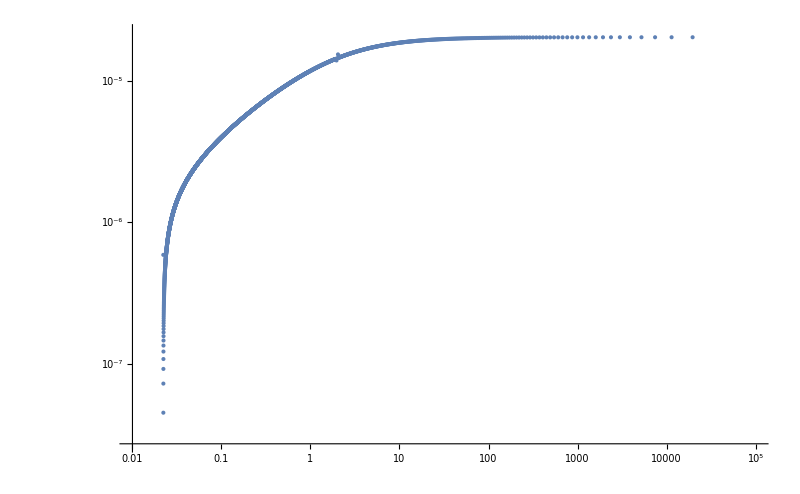

```mathematica
ListLogLogPlot[Abs[Re[listbeta]],PlotRange->{{1*10^-2,1*10^5},{0,2.2*10^-5}},ImageSize->800]
```

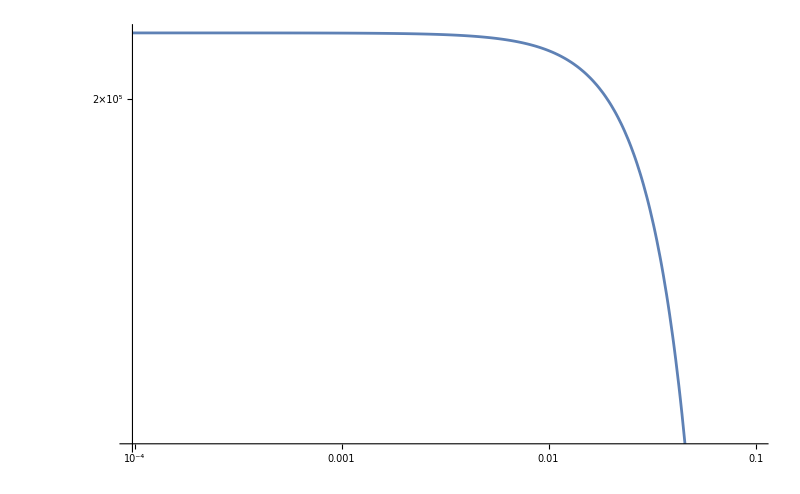

```mathematica
LogLogPlot[-Im[gammaincomp[ρ1,ρ2,U1,U2,kx,g,B]],{B,0,0.1},ImageSize->800]
```

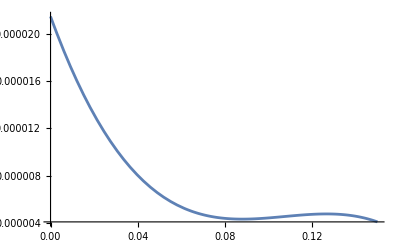

```mathematica
Plot[-0.01519*x^3+0.00489*x^2-0.0005077*x+2.148*10^(-5),{x,0,0.15}]
```

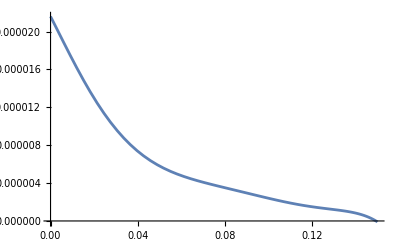

```mathematica
Plot[1.488*x^7-38.81*x^6+17.6*x^5-2.961*x^4+0.2068*x^3-0.002234*x^2-0.000449*x+2.16*10^(-5),{x,0,0.15}]
```

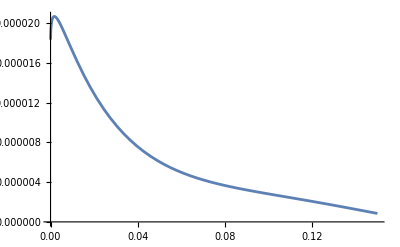

```mathematica
Plot[0.001613*x^(3/4)-0.00916x+0.01217x^3-0.01217x^2+0.01286x^(5/4)+1.834*10^(-5),{x,0,0.15}]
```

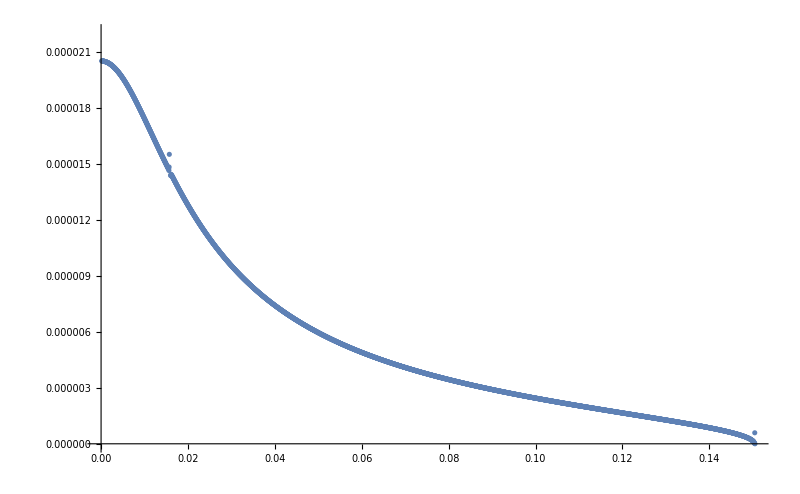

```mathematica
ListPlot[Abs[Re[list]],PlotRange->{{0,0.1505},{0,2.2*10^-5}},ImageSize->800]
```

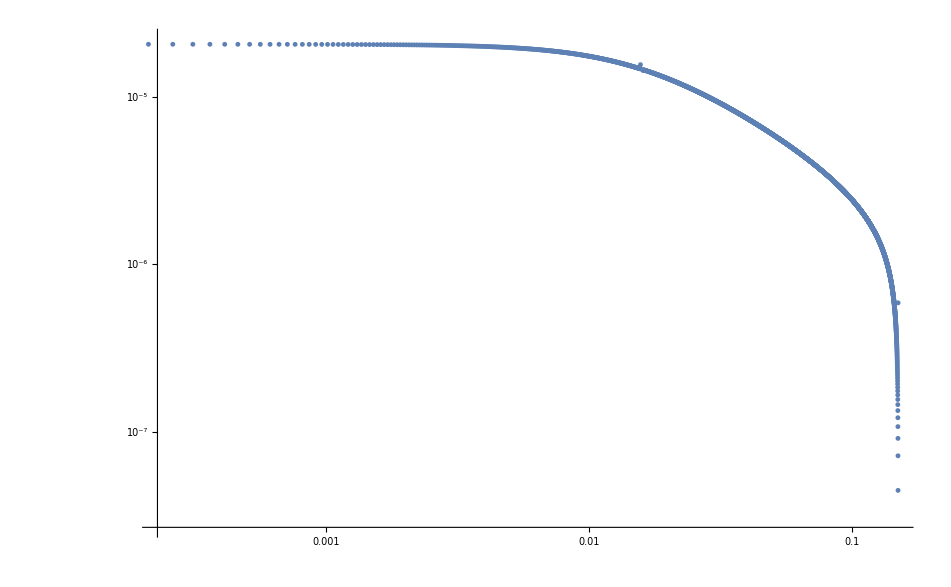

```mathematica
ListLogLogPlot[Abs[Re[list]],PlotRange->{{0,0.1505},{0,2.2*10^-5}}]
```

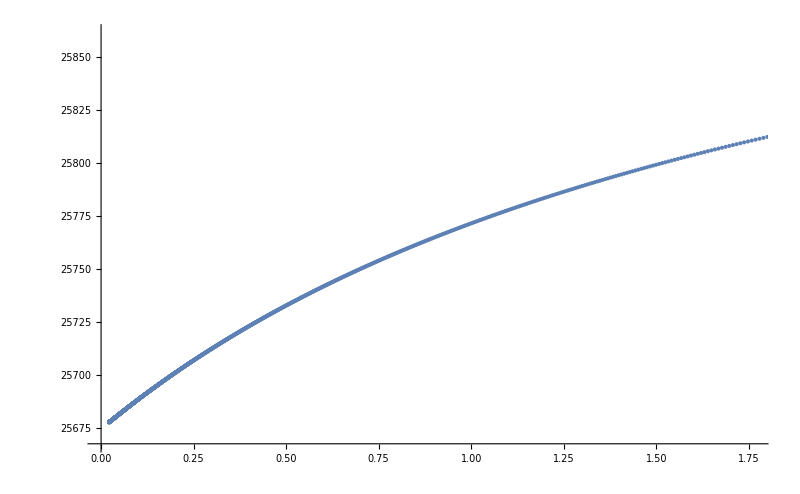

```mathematica
ListPlot[Abs[listbeta],ImageSize->800]
```

## Derivatives

We will look to see if we can find any information about the derivative of the growthrate as a function of the quantities of interest. NOPE

```mathematica
dispb = ReplaceAll[disprel[ρ1,ρ2,P,U1,U2,g,kx,ky,B,μ],{γ->γ[g]}];
```

```mathematica
D[dispb,g]
```